# Order parameters and χ4 for p0=3.80

## k is (2Pi,0)

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/localTest/2DmeltingPhase/N4096/p380/";
```

```mathematica
Tlist={0.063, 0.039 ,0.03105 ,0.025 ,0.016, 0.01 ,0.008 ,0.0063, 0.005 ,0.00385, 0.0031 ,0.0028,0.0025 ,0.0022};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000}

```mathematica
orientation=Table[Import[StringJoin[saveFolder,"orientationReIm_N4096_p3.800_T",Tstring[[T]],"_0.nc"],"Data"],{T,Length[Tlist]}];
```

```mathematica
translation=Table[Import[StringJoin[saveFolder,"otranslationReIm_N4096_p3.800_T",Tstring[[T]],"_0.nc"],"Data"],{T,Length[Tlist]}];
```

```mathematica
absOrientation=Table[Table[Sqrt[orientation[[T,1,i]]^2+orientation[[T,2,i]]^2],{i,Length[orientation[[T,1]]]}],{T,Length[Tlist]}];
```

```mathematica
absTranslation=Table[Table[Sqrt[translation[[T,1,i]]^2+translation[[T,2,i]]^2],{i,Length[orientation[[T,1]]]}],{T,Length[Tlist]}];
```

```mathematica
Dimensions[absOrientation]
```

{14,10000}

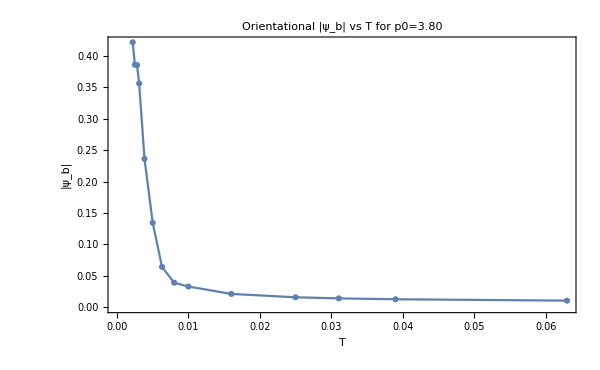

```mathematica
bondOrderPlot=ListPlot[Table[{Tlist[[T]],Mean[Normal[absOrientation[[T]]]]},{T,Length[Tlist]}],Joined->True,PlotMarkers->Automatic,FrameLabel->{"T","|ψ_b|"},ImageSize->600,PlotLabel->"Orientational |ψ_b| vs T for p0=3.80",PlotMarkers->Automatic]
```

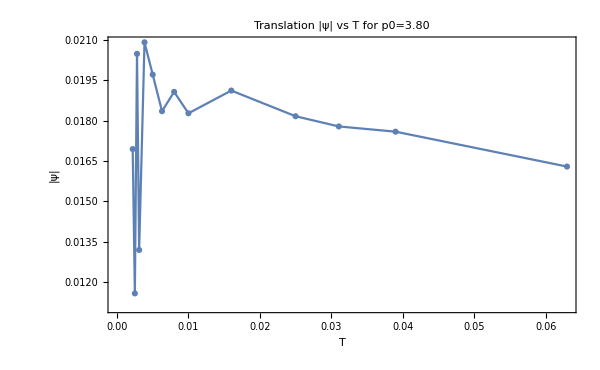

```mathematica
transOrderPlot=ListPlot[Table[{Tlist[[T]],Mean[Normal[absTranslation[[T]]]]},{T,Length[Tlist]}],Joined->True,PlotMarkers->Automatic,FrameLabel->{"T","|ψ|"},ImageSize->600,PlotLabel->"Translation |ψ| vs T for p0=3.80",PlotMarkers->Automatic]
```

```mathematica
4096*Variance[Normal[orientation[[15]]]]
```

0.649575

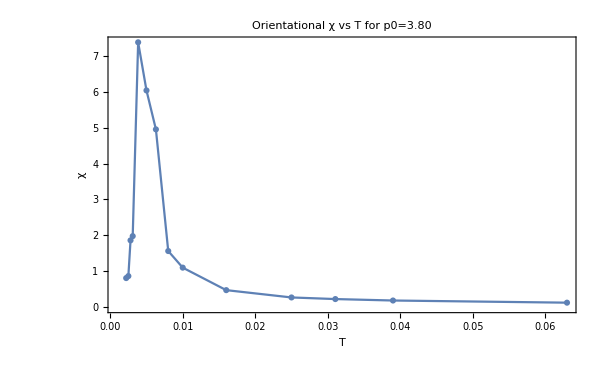

```mathematica
orientationchi4Plot=ListPlot[Table[{Tlist[[T]],4096*Variance[Normal[absOrientation[[T]]]]},{T,Length[Tlist]}],Joined->True,PlotRange->All,PlotMarkers->Automatic,FrameLabel->{"T","χ"},ImageSize->600,PlotLabel->"Orientational χ vs T for p0=3.80",PlotMarkers->Automatic]
```

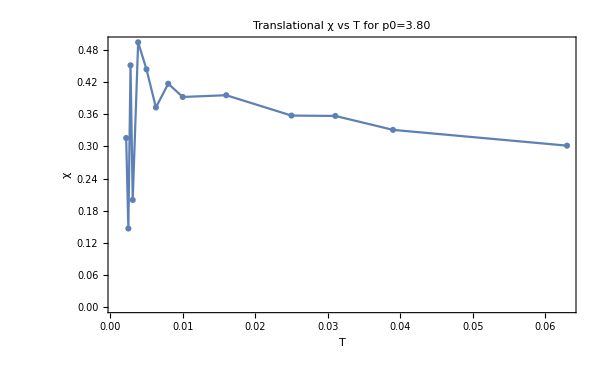

```mathematica
translationalChi4Plot=ListPlot[Table[{Tlist[[T]],4096*Variance[Normal[absTranslation[[T]]]]},{T,Length[Tlist]}],Joined->True,PlotRange->All,PlotMarkers->Automatic,FrameLabel->{"T","χ"},ImageSize->600,PlotLabel->"Translational χ vs T for p0=3.80",PlotMarkers->Automatic]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/orientationalchi4_p380.jpeg",orientationchi4Plot,ImageResolution->600];
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tranlationalchi4_p380.jpeg",translationalChi4Plot,ImageResolution->600];
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/bondorderParameter_p380.jpeg",bondOrderPlot,ImageResolution->600];
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/transorderParameter_p380.jpeg",transOrderPlot,ImageResolution->600];
```

```mathematica
absTranslation[[1]]
```

{0.0173007,0.0193727,0.00304264,0.0174723,0.0218506,0.0170284,0.00583736,0.0061906,0.00850299,0.0134738,0.0154247,0.00602046,0.0156235,0.00914005,0.0110191,0.0143946,0.0148888,0.0156209,0.0320752,0.030098,0.0246823,0.0122061,0.0204165,0.00488858,0.0258476,0.0372221,0.0192784,0.0153424,0.00929989,0.0174707,0.0208033,0.0150123,0.00836281,0.0075536,0.00397663,0.0156345,0.0195826,0.0273051,0.0289597,0.0181181,0.0119387,0.029755,0.0220212,0.00921743,0.00565768,0.0158315,0.0140617,0.00740597,0.0114214,0.0056626,0.00882661,0.00766476,0.0205798,0.0122456,0.0123697,0.00805345,0.0101576,0.00624986,0.0203436,0.0128247,0.0120515,0.0172202,0.0143463,0.0179282,0.0181769,0.01423,0.00913865,0.0088234,0.0234914,0.011237,0.0241513,0.0135343,0.0250638,0.0200438,0.0244786,0.0233186,0.00706453,0.025895,0.0154586,0.00249487,0.0102222,0.0151346,0.0139948,0.0231602,0.0230185,0.0238314,0.00543306,0.0208368,0.010481,0.0183787,0.0119978,0.00840974,0.00874326,0.0132383,0.00394738,0.00840018,0.0146642,0.00480371,0.0268693,0.021573,0.00289068,0.00719305,0.00881177,0.023679,0.017379,0.00314515,0.008729,0.00935618,0.0187735,0.0320033,0.0227016,0.00632273,0.0148832,0.00953544,0.0156314,0.0179081,0.0189014,0.0205613,0.0208288,0.01083,0.019938,0.0224644,0.00597451,0.0291617,0.0101703,0.00679429,0.0178544,0.0169318,0.0137876,0.0133824,0.00656344,0.0108931,0.0213418,0.0223935,0.0167152,0.0231396,0.00909114,0.00838756,0.00954431,0.039313,0.0100667,0.00814021,0.0289357,0.01857,0.0051335,0.0187363,0.0116692,0.00541039,0.0101451,0.0170458,0.0111801,0.0150407,0.0149159,0.0147956,0.0234434,0.00347789,0.0106674,0.0131832,0.00889544,0.0212475,0.0135555,0.0192804,0.00744873,0.0166069,0.0206531,0.00627441,0.0130188,0.00607921,0.0059621,0.00471382,0.00934545,0.00747698,0.0125983,0.00431995,0.0162465,0.0100032,0.0167985,0.0200812,0.0177078,0.0226985,0.00286892,0.0114693,0.020355,0.0112727,0.00732881,0.0121151,0.019359,0.0112036,0.0171919,0.0125661,0.037944,0.0233515,0.0221559,0.0114161,0.00690099,0.0159204,0.032877,0.0113957,0.0171053,0.0189365,0.0359263,0.0355904,0.0295433,0.0126436,0.00699867,0.0189838,0.0151722,0.00884957,0.026156,0.0291647,0.0135176,0.00468029,0.0128423,0.0146429,0.0246931,0.0139905,0.00747644,0.0240705,0.0251042,0.0330443,0.00743077,0.0163547,0.00951326,0.00760068,0.0207798,0.0163458,0.0173359,0.00167623,0.0292209,0.0125509,0.0116329,0.0271226,0.0213077,0.0253823,0.0178119,0.0212234,0.0106047,0.0115286,0.004511,0.00273297,0.0132956,0.031134,0.0186352,0.00996268,0.0146282,0.0157885,0.0221052,0.0244179,0.0111204,0.0160132,0.0233247,0.0224839,0.0254997,0.0186183,0.00896419,0.0307821,0.018711,0.0219817,0.0135032,0.00526921,0.0215035,0.0260902,0.0225342,0.0227119,0.0195126,0.0180456,0.0150512,0.0081741,0.0349445,0.000976217,0.0300838,0.0198289,0.00786668,0.0156627,0.00526202,0.0231604,0.00877868,0.0132199,0.0125743,0.00286459,0.00869982,0.0177653,0.0162328,0.0125711,0.0227298,0.0198518,0.00531165,0.0207756,0.0205106,0.0212821,0.0170552,0.0180723,0.0153637,0.0089346,0.0213356,0.0131787,0.00695758,0.0107519,0.00731721,0.0160505,0.0185727,0.0140406,0.00717081,0.00792767,0.0128697,0.0182811,0.0126696,0.00730202,0.00668995,0.0110603,0.0075113,0.0125688,0.0278471,0.0275115,0.0202675,0.00415669,0.00581738,0.0201849,0.0303953,0.00688073,0.0126674,0.0130627,0.0118659,0.0124449,0.018085,0.0254955,0.0151012,0.0151879,0.0105588,0.00882097,0.00952317,0.0152687,0.00235154,0.0170893,0.00625725,0.0324588,0.0261965,0.0227427,0.0402907,0.0618822,0.0307287,0.0269522,0.012269,0.00794385,0.00506042,0.00357196,0.0245512,0.00806624,0.0083527,0.0192235,0.0296621,0.0223016,0.0282516,0.0112726,0.00633029,0.0151937,0.00732996,0.0329901,0.0239842,0.0232474,0.0108693,0.023289,0.0186282,0.0292542,0.0364818,0.00792164,0.0126584,0.0080369,0.0115348,0.00177907,0.0151923,0.0153628,0.00866463,0.0128347,0.0165082,0.015237,0.0121048,0.0109562,0.0192084,0.0176863,0.0131177,0.00508505,0.00747564,0.0197661,0.0217149,0.0346415,0.0151486,0.00854784,0.00657912,0.00790156,0.015282,0.0200965,0.0184701,0.0166412,0.0183142,0.00658533,0.00611382,0.0103759,0.0124214,0.0089279,0.0110795,0.0320508,0.0241771,0.0109179,0.0103629,0.0177039,0.0247995,0.00788656,0.00332773,0.0109298,0.0120666,0.0129137,0.00310266,0.00981504,0.0103625,0.0104337,0.0153667,0.00345922,0.0195479,0.0391819,0.0163086,0.0192688,0.00435227,0.0140473,0.0159687,0.0166193,0.0169221,0.0102944,0.018529,0.00449777,0.0211406,0.00726447,0.00423526,0.00626081,0.0126343,0.00531959,0.0107737,0.0288373,0.00996896,0.0177927,0.0354368,0.0337941,0.00729863,0.0246982,0.00714661,0.0139091,0.0057891,0.0344229,0.0162648,0.00581221,0.00806962,0.0148474,0.0137348,0.0124222,0.0286191,0.0412607,0.029356,0.0201706,0.006024,0.00464629,0.0119366,0.0260518,0.0240024,0.0459469,0.0379272,0.0203986,0.0117898,0.0211845,0.0190315,0.01263,0.0147533,0.0127521,0.0180739,0.025845,0.0319581,0.00903362,0.0113107,0.0215474,0.0160688,0.0103341,0.0127856,0.0188667,0.0188644,0.0256082,0.0211834,0.0315994,0.0116985,0.0182382,0.0232329,0.0221497,0.0200592,0.00600418,0.00749075,0.00296543,0.013808,0.0249986,0.0199059,0.0133805,0.0150521,0.00127399,0.0212521,0.0273312,0.0224925,0.0168821,0.0269541,0.0156955,0.0209891,0.0243508,0.00254787,0.0223191,0.0072616,0.0176441,0.0137864,0.0109662,0.00783137,0.00890953,0.0144875,0.0221309,0.0154204,0.00716564,0.0151549,0.00712321,0.022979,0.00890956,0.00886939,0.0093772,0.00459514,0.0140023,0.0219401,0.0188357,0.00260669,0.0249402,0.0207735,0.0176062,0.0101823,0.0218885,0.0141331,0.00356551,0.0068776,0.014115,0.0160064,0.0148836,0.0257605,0.0107332,0.0148826,0.0166857,0.016728,0.0328062,0.0195353,0.0159866,0.0299989,0.0249593,0.00275012,0.0279835,0.0043629,0.0096256,0.0138663,0.0156917,0.0133864,0.0163838,0.0166392,0.00234481,0.0346381,0.0302367,0.0119349,0.0208294,0.0433329,0.0197662,0.0117387,0.01926,0.00420468,0.0144829,0.0145616,0.00791456,0.0207566,0.0290176,0.0248015,0.012682,0.0189463,0.0214389,0.011193,0.0153885,0.029296,0.0289521,0.0150491,0.0161351,0.0121012,0.0100496,0.00717687,0.00459852,0.0184807,0.0115688,0.011386,0.00730881,0.00414988,0.0119291,0.0229734,0.019612,0.0146027,0.0112722,0.0112284,0.00188457,0.0212614,0.0263197,0.0259771,0.0167813,0.0164625,0.0183995,0.0153048,0.0397389,0.0306575,0.0207622,0.0121044,0.00856326,0.00941849,0.0303628,0.034999,0.0190226,0.0151118,0.0298532,0.0389296,0.0260952,0.00544972,0.00616621,0.0147545,0.00682475,0.0189089,0.0132103,0.0168334,0.0305134,0.0121271,0.0171401,0.0195595,0.0231603,0.00903645,0.00887032,0.0143767,0.0217097,0.0239053,0.0113408,0.00718172,0.00986994,0.00059546,0.00899364,0.0196644,0.00596847,0.0111123,0.0128754,0.032065,0.0275942,0.00119277,0.0122877,0.0316488,0.0164184,0.0249323,0.00623129,0.0293797,0.0190652,0.011835,0.0173577,0.0139062,0.0233686,0.0103656,0.0118966,0.00982704,0.0153898,0.0160937,0.0281233,0.00144895,0.00689462,0.0108803,0.0124543,0.00639166,0.0174376,0.021847,0.0138813,0.00561663,0.0101997,0.0167916,0.0039123,0.0297374,0.0339265,0.011319,0.0187843,0.0278883,0.00536795,0.0126556,0.00986753,0.0133767,0.0129148,0.00716808,0.0078202,0.0108816,0.00789143,0.00783624,0.00495315,0.012485,0.00601363,0.0265955,0.0104616,0.0237021,0.0177637,0.0111446,0.034105,0.0222411,0.029452,0.00977854,0.0217851,0.021482,0.0223624,0.0187075,0.021234,0.0157543,0.00890105,0.00835396,0.0314762,0.0241259,0.00238532,0.0210507,0.0226149,0.0294193,0.0183344,0.00422932,0.0207299,0.0137193,0.0167032,0.0194935,0.00222547,0.00935634,0.0270912,0.0141798,0.00557056,0.0131869,0.0104388,0.00822399,0.0158911,0.0090185,0.00860917,0.0116736,0.0116862,0.0194732,0.0194682,0.0175783,0.015396,0.0206132,0.0124942,0.0290341,0.0331156,0.00895265,0.0111969,0.00958471,0.00592275,0.0123414,0.0121073,0.0286244,0.0148352,0.0217237,0.0255143,0.0223021,0.0245383,0.0203169,0.0136794,0.0212804,0.0203509,0.011301,0.0257051,0.0390117,0.0241412,0.0194063,0.0192015,0.0338211,0.0041551,0.00680004,0.028404,0.0123809,0.0061703,0.00623289,0.018717,0.017649,0.0222227,0.0174643,0.012824,0.0256135,0.0139809,0.0264494,0.0238079,0.0150602,0.00202719,0.00307625,0.0184158,0.0232614,0.0273645,0.018134,0.00873287,0.015483,0.0225209,0.0143064,0.0155474,0.0123225,0.0105255,0.0194504,0.0102412,0.00868098,0.0237018,0.01045,0.00809763,0.00970995,0.0199207,0.0337881,0.033768,0.0164434,0.0277408,0.0193621,0.00985613,0.00320994,0.00790696,0.0145704,0.0179984,0.012451,0.0301629,0.0112812,0.023879,0.0102459,0.00675266,0.00626552,0.015941,0.0207413,0.0103729,0.0120295,0.00763311,0.0248355,0.00933858,0.0155915,0.01416,0.00814953,0.0336048,0.00593554,0.0290647,0.0229207,0.00716536,0.00495989,0.0197909,0.0132712,0.0220703,0.0237617,0.00101893,0.0128111,0.0167844,0.0302271,0.00781643,0.0120921,0.00946736,0.0176652,0.00649832,0.00729572,0.0117954,0.0252281,0.0259839,0.0127648,0.0117973,0.0193766,0.0105498,0.0163446,0.00952614,0.00643118,0.0220549,0.00915538,0.00311563,0.0173283,0.0249887,0.0139984,0.0169948,0.00910039,0.0122266,0.0235592,0.0216875,0.0109939,0.0185768,0.013218,0.0116885,0.0208172,0.0182284,0.00919673,0.00722239,0.00956261,0.00733894,0.0134381,0.0120061,0.00505574,0.0015408,0.0258813,0.0240824,0.0149485,0.0101227,0.0164463,0.0108801,0.0207557,0.0178368,0.00964745,0.0112772,0.017831,0.0248817,0.030247,0.0227699,0.0113205,0.00839571,0.0179597,0.00853088,0.00864234,0.0191608,0.0103759,0.00845442,0.00863341,0.0215255,0.00872497,0.00304514,0.00900803,0.0164939,0.0197811,0.0175435,0.0124496,0.00288762,0.0326306,0.022724,0.0188356,0.0195562,0.0259697,0.00569895,0.0300178,0.0214478,0.0113227,0.000617043,0.00560581,0.0152287,0.0141236,0.0183144,0.011034,0.0163126,0.0117301,0.0112299,0.0215239,0.024155,0.0191887,0.00917334,0.00475553,0.00631724,0.0117566,0.0141357,0.00919105,0.00589399,0.0173941,0.00803358,0.0110034,0.0182296,0.0124321,0.0095866,0.0216146,0.00997001,0.00366828,0.0169188,0.0117115,0.0107144,0.0156467,0.0049864,0.0228984,0.025162,0.0278666,0.0230069,0.0197691,0.0171361,0.0283438,0.0140673,0.0220051,0.0190619,0.0202404,0.0260375,0.0255009,0.0257845,0.0105505,0.0194127,0.0130217,0.0171504,0.00936285,0.00855858,0.00526512,0.00641544,0.0253789,0.023016,0.027161,0.0268527,0.0226705,0.0145639,0.0108174,0.0125695,0.0124568,0.0291769,0.0164031,0.00332412,0.011985,0.0185332,0.00509868,0.00933211,0.0222476,0.0194435,0.018751,0.0172056,0.0180951,0.00438057,0.0132465,0.0226367,0.00759807,0.023213,0.0222701,0.00858277,0.0255418,0.0136291,0.0236766,0.00864492,0.018238,0.031192,0.0151646,0.0122413,0.012622,0.0227193,0.00679497,0.0126477,0.00993282,0.00219931,0.00486439,0.0191482,0.0287235,0.0168602,0.0259702,0.00948595,0.012969,0.0294839,0.0430254,0.0319677,0.024835,0.0133924,0.00863229,0.0176623,0.0237433,0.0193026,0.00976114,0.0117544,0.0129125,0.0237408,0.0170352,0.00921104,0.00936664,0.0183318,0.014605,0.00352662,0.0186099,0.0208757,0.02092,0.0199778,0.0306519,0.00945879,0.00384847,0.0177342,0.0110363,0.00572799,0.0206887,0.0127804,0.0216117,0.0112277,0.0133832,0.0179183,0.00644488,0.00812024,0.0142383,0.0270731,0.0318984,0.0163019,0.0203508,0.0175353,0.0127965,0.0161213,0.0160913,0.0150934,0.0141929,0.0147622,0.00719506,0.0202872,0.0113891,0.0263928,0.0253998,0.0180763,0.0082708,0.00915768,0.00786611,0.0172526,0.0119461,0.00832229,0.00383011,0.031106,0.0366713,0.0492032,0.0378269,0.0382005,0.0265886,0.0111817,0.0122041,0.0166089,0.0156892,0.00560248,0.0208235,0.0243093,0.0124785,0.00663022,0.0123726,0.0164333,0.0029317,0.00893597,0.0210609,0.0128948,0.00717004,0.0128774,0.0252225,0.0116467,0.00997543,0.0125701,0.0116317,0.00637439,0.0117489,0.0153108,0.021678,0.0286,0.00242252,0.00128278,0.00486162,0.00731724,0.00235773,0.0118691,0.0053052,0.00771402,0.01003,0.0265738,0.0100865,0.0241025,0.0103267,0.0100082,0.0244794,0.00645447,0.0153505,0.0100365,0.00974747,0.0224029,0.0261674,0.0139094,0.0155492,0.00707807,0.014494,0.0194625,0.0153927,0.0122155,0.0189374,0.0140147,0.00953805,0.0190815,0.0185473,0.0241214,0.014924,0.0100924,0.0132304,0.00372881,0.00663805,0.00929006,0.0106887,0.0136645,0.0161472,0.0296771,0.0315266,0.0227177,0.0171165,0.0155586,0.00393124,0.00825835,0.0105063,0.0283325,0.0148328,0.0194574,0.0127811,0.013282,0.0164534,0.0235449,0.0115179,0.0165707,0.00456795,0.00806366,0.0114088,0.00256349,0.0181739,0.0133907,0.0222442,0.00869644,0.00664585,0.0105978,0.0146145,0.0131899,0.0129896,0.0155517,0.0187695,0.0197062,0.0226495,0.033776,0.0203855,0.0231983,0.0178888,0.0258225,0.0201572,0.0110643,0.0160324,0.00163152,0.0185262,0.0318383,0.0129064,0.0209529,0.00390031,0.013941,0.0151118,0.0135577,0.0225054,0.01166,0.00930728,0.0182352,0.0116346,0.0213501,0.0177422,0.00524236,0.00885913,0.0164399,0.00213331,0.0160353,0.0371399,0.0316471,0.0256423,0.0160861,0.0191469,0.0247411,0.0205864,0.0157798,0.00251389,0.0290788,0.0146776,0.0110626,0.00983774,0.00834227,0.00313593,0.0170595,0.00585553,0.00483652,0.0120135,0.0189662,0.00932176,0.00851229,0.00629522,0.00282283,0.0163496,0.00148142,0.0139032,0.0119144,0.0158798,0.026859,0.00473898,0.0133105,0.00851844,0.0291575,0.014147,0.0177532,0.00581771,0.00524047,0.00841143,0.0181548,0.0158169,0.0249282,0.00605611,0.00821702,0.0246531,0.00554021,0.00631362,0.0118497,0.0126993,0.0173672,0.00633255,0.0169192,0.00934431,0.0140207,0.00287025,0.0152808,0.0180699,0.00353833,0.0165238,0.0128179,0.0165324,0.0194309,0.0344853,0.00931045,0.0196516,0.0317717,0.0254087,0.00636331,0.0108681,0.0116226,0.00782645,0.012395,0.0244,0.0162353,0.00216954,0.00993307,0.00494777,0.0060154,0.0201239,0.00472382,0.00286319,0.0109742,0.0232165,0.0274602,0.00987597,0.0122886,0.00815116,0.0339429,0.0250624,0.00653593,0.00213062,0.00544034,0.00971138,0.0218016,0.019466,0.00759993,0.0164132,0.0141749,0.019541,0.0131894,0.0236987,0.0329128,0.0346933,0.0327021,0.00678256,0.0296315,0.0116248,0.0209542,0.00593552,0.0132627,0.0139033,0.0111115,0.0177779,0.014837,0.00254763,0.0112591,0.0189796,0.028539,0.0195044,0.0222543,0.00697002,0.00639267,0.0146355,0.0158284,0.00754501,0.00491009,0.0115872,0.007533,0.00665092,0.0101308,0.0109728,0.00720987,0.00568555,0.00104861,0.0182262,0.0280794,0.0132173,0.0169717,0.0268106,0.0215038,0.00864815,0.0137149,0.00564237,0.0194257,0.0203301,0.0281781,0.0289466,0.0359617,0.0189774,0.00651404,0.0121153,0.0194321,0.0171646,0.0315463,0.0201594,0.00900104,0.00747948,0.0221816,0.0266209,0.0201884,0.0136709,0.00692419,0.0185607,0.00531378,0.0162037,0.0233737,0.0160062,0.00805315,0.0106519,0.0176921,0.0158327,0.0195922,0.0163931,0.00956793,0.0122236,0.0138228,0.0121702,0.015059,0.00970391,0.00809554,0.00840252,0.0185515,0.0148635,0.0170629,0.0128621,0.0226346,0.00845042,0.0048499,0.00741449,0.0356199,0.0163491,0.0170469,0.0135531,0.00748523,0.00400046,0.0276709,0.0100726,0.0153424,0.0133541,0.0328765,0.0364406,0.0357353,0.0356766,0.0285442,0.0158847,0.0186833,0.0100243,0.0347313,0.01441,0.00530407,0.0068693,0.0190299,0.0167418,0.0127782,0.00550452,0.0189664,0.0191482,0.0232036,0.00731238,0.00613767,0.0139848,0.0290509,0.00164428,0.0111111,0.00256822,0.00537976,0.0209539,0.0140209,0.0131846,0.00255622,0.00499752,0.0131493,0.0390877,0.0188603,0.018109,0.0308276,0.0272406,0.031986,0.0156157,0.00589155,0.0195085,0.0104775,0.00613166,0.0157995,0.0263901,0.038319,0.0170701,0.012945,0.0299598,0.00702162,0.00491146,0.0122665,0.015373,0.0110424,0.0331934,0.0120296,0.00420796,0.0210512,0.00754303,0.00809921,0.027717,0.0267074,0.0150981,0.0199232,0.00878874,0.0179168,0.0241818,0.0171337,0.020459,0.0130049,0.00925992,0.0117233,0.0261091,0.0134679,0.0141975,0.0157639,0.0146184,0.0131902,0.00511243,0.0153974,0.00749651,0.00944449,0.0152153,0.0128713,0.0148788,0.0261871,0.01585,0.00806008,0.00454032,0.0207424,0.00579557,0.00660647,0.012888,0.0236047,0.0108583,0.00874323,0.0129094,0.0175869,0.0129712,0.00951071,0.0217868,0.0276878,0.0183146,0.0300507,0.0196539,0.0105803,0.0142752,0.0176405,0.0197842,0.024142,0.0156089,0.018146,0.0203907,0.00811202,0.0198026,0.0186991,0.0111978,0.00816239,0.0171746,0.0428528,0.0263891,0.0243023,0.0184209,0.0114357,0.0214856,0.0187766,0.0202267,0.023688,0.0320918,0.0120155,0.00764863,0.0135366,0.0149227,0.017187,0.0107524,0.00818465,0.0184715,0.0246594,0.0077946,0.0110126,0.00359563,0.00548091,0.00516189,0.0155875,0.017087,0.0267633,0.0191791,0.0101343,0.0121797,0.010336,0.0178676,0.0134812,0.0046289,0.0162832,0.00957721,0.00909697,0.0152898,0.010548,0.0214099,0.0377951,0.0222777,0.00930774,0.0159278,0.0236379,0.0165943,0.00920111,0.0187648,0.00659415,0.00298665,0.0219268,0.0110857,0.0299669,0.00974406,0.0172105,0.00198899,0.00927846,0.0272476,0.0183358,0.0227751,0.0178841,0.030233,0.0171832,0.00833135,0.0134957,0.0244104,0.0326192,0.0210085,0.00916445,0.0179131,0.0292414,0.0313264,0.0222747,0.0148708,0.0121774,0.0152284,0.0149529,0.00746936,0.0156772,0.00885844,0.0328854,0.0130856,0.0119157,0.0113388,0.00963113,0.0333035,0.0226046,0.0187074,0.0114808,0.0133996,0.0244554,0.0240354,0.0206646,0.0205421,0.0202402,0.0161834,0.0190649,0.0226095,0.0181883,0.0065937,0.00937199,0.00999626,0.0137217,0.0226382,0.0208255,0.0124179,0.0253758,0.0121383,0.0110955,0.0126238,0.00695951,0.0103256,0.00593963,0.013295,0.0074142,0.00361781,0.00322972,0.0145565,0.00815433,0.0384016,0.0429161,0.0328632,0.0251323,0.00288928,0.0146737,0.0111357,0.0250379,0.0215859,0.0353281,0.0296339,0.0117055,0.0328042,0.0268417,0.0336346,0.027233,0.00748883,0.0194066,0.00874926,0.0151483,0.0116396,0.0291852,0.0313556,0.0158355,0.0164728,0.0184005,0.0173687,0.0153186,0.0179274,0.0177275,0.00911894,0.0122276,0.0211848,0.019317,0.0144049,0.0126443,0.0186555,0.00821082,0.0114626,0.0294584,0.0226141,0.0129167,0.0153329,0.00472679,0.0237943,0.0153372,0.0122561,0.00635242,0.0174198,0.00994161,0.00886003,0.0202624,0.0128428,0.00921691,0.00923014,0.00396479,0.013804,0.0139298,0.0144972,0.00458401,0.052771,0.0190575,0.0124978,0.0120094,0.0114579,0.0196246,0.0176392,0.00842415,0.0184709,0.0120052,0.0260502,0.0238101,0.00769134,0.00563228,0.00886208,0.00363912,0.00984799,0.00822949,0.0111412,0.00768138,0.0102192,0.0232452,0.0222712,0.0196202,0.0214007,0.0122161,0.0048968,0.0169749,0.00974384,0.0126423,0.0218149,0.0261007,0.0170769,0.0153929,0.0205494,0.00167047,0.0109033,0.0136157,0.00814599,0.0154134,0.00565779,0.00295868,0.0173088,0.0148626,0.0145894,0.00275054,0.0177797,0.0241612,0.00915451,0.0259624,0.0204468,0.0162117,0.0143185,0.0107624,0.01432,0.0269286,0.00985114,0.0090211,0.017079,0.0335381,0.00628755,0.0101438,0.0237921,0.0104456,0.00592232,0.00528599,0.0231749,0.0093004,0.017418,0.0094223,0.0212226,0.00839555,0.0157351,0.0357636,0.0240037,0.00912972,0.0188645,0.0108785,0.0135588,0.0338886,0.0167525,0.00271964,0.0125051,0.0272224,0.00925845,0.00844594,0.0218045,0.0292222,0.0145716,0.0194535,0.00971301,0.00565117,0.0232262,0.0195608,0.0119342,0.0251203,0.0199451,0.02115,0.0252538,0.0257843,0.0232857,0.0172549,0.00173274,0.0218509,0.0202301,0.0262997,0.0114476,0.00758423,0.00245604,0.0101091,0.0187883,0.0170679,0.0171831,0.0218439,0.0196968,0.0060151,0.0130863,0.0111351,0.00652623,0.018852,0.0286442,0.00940167,0.0144313,0.0106103,0.0025104,0.0147708,0.0234339,0.017117,0.00458226,0.00498442,0.00487653,0.00996015,0.0211252,0.0185703,0.0171809,0.0124508,0.018442,0.0230279,0.00859959,0.0115764,0.00508613,0.0170562,0.0150461,0.0260449,0.00286741,0.0317701,0.0178267,0.0167683,0.0247053,0.0335831,0.0309205,0.0113786,0.0170321,0.013578,0.0233459,0.0295996,0.0374592,0.0116005,0.00215163,0.00384215,0.0106569,0.00574729,0.00539558,0.0115586,0.0137638,0.0202129,0.0205684,0.00857878,0.0165562,0.0348601,0.0239674,0.0204235,0.0210002,0.0199523,0.0144166,0.0197538,0.00377671,0.00619084,0.020842,0.0188305,0.0167617,0.0237338,0.0154426,0.0167321,0.019412,0.00207604,0.00607643,0.0128983,0.0163846,0.0138093,0.0313393,0.0169738,0.0199115,0.0166841,0.0204079,0.0114097,0.0102863,0.00525307,0.0134358,0.00949788,0.010603,0.0199707,0.0306718,0.0257977,0.0124114,0.0138625,0.0125412,0.0107626,0.00837045,0.0176193,0.0146696,0.01508,0.0147445,0.0189994,0.013893,0.00995605,0.00625197,0.0239841,0.0336054,0.0363028,0.0193378,0.00147234,0.0182512,0.0139493,0.00446061,0.00787859,0.0137374,0.0192389,0.0300676,0.0193452,0.0215409,0.0338306,0.0202513,0.0240278,0.026799,0.0202863,0.0150527,0.013662,0.00325853,0.0232109,0.0083802,0.0104375,0.0223784,0.0401315,0.0226987,0.0275001,0.0253155,0.0102048,0.00802316,0.00548318,0.0305466,0.0375352,0.0261289,0.00823918,0.00976262,0.0152208,0.016227,0.0155081,0.00141378,0.00889256,0.00710304,0.00567161,0.00318493,0.0118995,0.0171921,0.0136327,0.00407942,0.0279031,0.0136452,0.00905363,0.0290908,0.0134302,0.0224759,0.00842021,0.0135685,0.0093382,0.0116441,0.0181488,0.0226379,0.00675855,0.0157573,0.0132727,0.0171272,0.00804718,0.0146368,0.0212003,0.0276251,0.0317783,0.0286651,0.01322,0.00869587,0.00409602,0.0176075,0.0127616,0.00935987,0.012665,0.0159453,0.00706895,0.00556172,0.0185337,0.01243,0.0159834,0.0125241,0.0221989,0.0159777,0.0260178,0.00670764,0.0111772,0.0216396,0.0253236,0.00930667,0.0232435,0.00329838,0.0197032,0.0173798,0.0153986,0.0122438,0.0291282,0.0230588,0.0227038,0.028231,0.0206148,0.0247545,0.031425,0.0340374,0.0182596,0.00727399,0.0110731,0.0223452,0.0285807,0.0129099,0.012637,0.0145759,0.0158393,0.0230416,0.0183218,0.0118445,0.00802287,0.0353982,0.0225569,0.0367728,0.0240774,0.0286711,0.0103724,0.00205861,0.00796203,0.0345663,0.0243661,0.00840274,0.00642765,0.0165847,0.0171048,0.0160218,0.0370638,0.00274835,0.0052409,0.00902002,0.0168661,0.0125306,0.00702817,0.0206293,0.0157102,0.0160554,0.0272238,0.0145244,0.0246253,0.00159907,0.0118703,0.017851,0.00706463,0.00641052,0.014846,0.0072127,0.0130578,0.0129045,0.0115483,0.00828977,0.0229086,0.0172224,0.0262666,0.0259979,0.0180064,0.0394656,0.0344812,0.0120881,0.0140739,0.0157692,0.0282967,0.0373437,0.0280448,0.0255927,0.0188331,0.0198803,0.0276242,0.0306008,0.00884227,0.0135117,0.0138498,0.0173524,0.0025129,0.00962429,0.0186303,0.0315575,0.0315972,0.0159173,0.0126781,0.0178174,0.00919624,0.0137125,0.00171897,0.00685252,0.0101427,0.0111545,0.0178979,0.0157063,0.0114291,0.0285643,0.0200444,0.0161916,0.0157755,0.029017,0.0152582,0.00112603,0.0227371,0.0207171,0.0221828,0.0199262,0.00966237,0.0251786,0.0112406,0.00240098,0.0216483,0.0161532,0.00746096,0.00364766,0.0093733,0.00909901,0.0314128,0.0296715,0.0198815,0.003365,0.00963851,0.0158904,0.00152213,0.0160612,0.0305785,0.011896,0.0198291,0.0258841,0.0362384,0.0269216,0.00353767,0.00726764,0.00645384,0.0156834,0.0181802,0.0100042,0.0176128,0.00826438,0.0135269,0.0087269,0.00920137,0.0228841,0.0173491,0.0194078,0.0111838,0.00925881,0.0106574,0.0130137,0.012224,0.0104365,0.0170704,0.0149483,0.0164333,0.0386561,0.0355461,0.0237181,0.00780538,0.00940028,0.0171186,0.00695321,0.0220474,0.0220533,0.0254175,0.0124754,0.014467,0.0246963,0.0329812,0.0252712,0.0200889,0.0224384,0.0105234,0.00559952,0.0203612,0.0213313,0.0167341,0.0122895,0.0124909,0.0186042,0.0163957,0.0129266,0.011075,0.0159468,0.00482314,0.0231931,0.040858,0.0125648,0.00260794,0.0182642,0.00439919,0.00428376,0.0062766,0.00516255,0.00725951,0.0038933,0.00331664,0.00967867,0.0105063,0.0124574,0.0092612,0.0139551,0.00480344,0.019394,0.0135698,0.0172742,0.0240404,0.0168934,0.0124088,0.0114883,0.0300739,0.0291176,0.000815573,0.0235468,0.0214222,0.00879264,0.0149849,0.0236936,0.00821738,0.0181606,0.0130134,0.0145405,0.00927808,0.01413,0.0288368,0.0264531,0.00214164,0.0223206,0.0369798,0.040789,0.0164343,0.0117019,0.0118825,0.0285355,0.0177454,0.00641551,0.0116611,0.020571,0.0342783,0.0356636,0.0137328,0.0204537,0.0213095,0.00694713,0.00936906,0.0149511,0.0114742,0.0222301,0.0203939,0.0231134,0.0220694,0.00954577,0.0176672,0.021266,0.0227187,0.0180095,0.00595477,0.0328201,0.0253875,0.0269481,0.019183,0.0119735,0.00632189,0.014205,0.00684936,0.00714345,0.0134485,0.019187,0.0203643,0.00540705,0.0103712,0.0125509,0.0109683,0.00532409,0.0174078,0.0276507,0.0354198,0.0121544,0.00665876,0.0137797,0.0177033,0.0141608,0.00491885,0.0135199,0.0127462,0.0258464,0.0222743,0.0147071,0.0318379,0.0408193,0.019535,0.00764059,0.0179587,0.0200616,0.0314332,0.00413384,0.0121629,0.0285884,0.0221481,0.013983,0.0202878,0.0132112,0.0158317,0.0192534,0.0225267,0.0145045,0.0116129,0.00599166,0.0189581,0.0145014,0.0246118,0.0180279,0.0185938,0.0179989,0.0134479,0.0146594,0.00444967,0.00958399,0.00567618,0.010476,0.00818711,0.0233723,0.0290375,0.0178705,0.00706709,0.0100262,0.0409094,0.0235126,0.0187785,0.00530813,0.0118423,0.0294124,0.0207294,0.00834419,0.00522052,0.0185297,0.0153152,0.0128786,0.00513765,0.00716305,0.0273126,0.0164296,0.00941628,0.00463088,0.0264353,0.0149024,0.0305821,0.0310099,0.0283347,0.0210725,0.0165189,0.0177619,0.0101323,0.00322843,0.0230424,0.0198761,0.00972179,0.0252779,0.0137016,0.00713221,0.0161364,0.00905384,0.00795353,0.0238226,0.0232189,0.011378,0.00751139,0.0173671,0.0254117,0.020571,0.0278282,0.0206246,0.0259211,0.0277144,0.018746,0.00227552,0.0256119,0.0185601,0.0230284,0.00878736,0.0156685,0.0161902,0.0274701,0.0268329,0.00427104,0.0133264,0.0385668,0.0312889,0.0301417,0.0186023,0.0298986,0.0239813,0.0170442,0.0113281,0.00145079,0.00247626,0.017133,0.0187265,0.00640239,0.0171133,0.0166534,0.0066501,0.00818956,0.0138746,0.0143711,0.00537997,0.0135719,0.0101599,0.00583716,0.0250657,0.0202974,0.0291298,0.0225536,0.00567292,0.0148392,0.00743205,0.0090304,0.00625644,0.01235,0.0189759,0.0156357,0.0222154,0.0222524,0.0211558,0.0187279,0.0217737,0.0247473,0.0230696,0.0221143,0.0167733,0.0125139,0.0109258,0.00886953,0.0102705,0.0141274,0.0237571,0.0144241,0.0186563,0.0173472,0.0235685,0.0317762,0.0105277,0.016979,0.0114736,0.00499749,0.027441,0.0232991,0.00858277,0.00132221,0.0222819,0.0125802,0.0165837,0.00704034,0.0113676,0.000813537,0.0289648,0.0111847,0.00866606,0.00535931,0.0105104,0.00499602,0.0133697,0.0282612,0.033971,0.0183451,0.0234689,0.0154876,0.0178889,0.0226934,0.0205033,0.0246804,0.0108487,0.00454653,0.0123328,0.00485382,0.0293646,0.0521076,0.0462819,0.033291,0.0248512,0.0367939,0.0225336,0.0304309,0.0281758,0.00612246,0.0155121,0.00866147,0.00908042,0.0193925,0.0197714,0.00719151,0.0194802,0.00920999,0.0220132,0.00357732,0.0173986,0.0123163,0.00155692,0.0239626,0.00752067,0.0141706,0.0111928,0.0434548,0.030754,0.00434238,0.0148974,0.0104618,0.0157331,0.0159725,0.0129257,0.017763,0.0172253,0.00685585,0.0138973,0.00872821,0.0110724,0.00198717,0.0241075,0.0241676,0.0400564,0.0269347,0.0117776,0.0106132,0.0102244,0.00274283,0.00840311,0.0117204,0.0122236,0.00251981,0.00949747,0.0166172,0.00536214,0.0256451,0.0168039,0.00771554,0.011437,0.0206497,0.00757626,0.00729636,0.00740708,0.0185866,0.0136522,0.00737194,0.0125734,0.0140922,0.0189785,0.0170574,0.0242844,0.0128514,0.00454044,0.0146526,0.0247117,0.0194728,0.025936,0.0279263,0.0125317,0.0068572,0.0122742,0.0066934,0.00973382,0.0119777,0.00468919,0.00953486,0.022657,0.0196842,0.0174409,0.0285389,0.00952852,0.0169221,0.0195832,0.0068453,0.00828286,0.00594386,0.0243217,0.029273,0.0085109,0.00674837,0.00990232,0.00492904,0.0131722,0.0209134,0.0195754,0.00998084,0.0137602,0.00304154,0.0101445,0.00939529,0.0146759,0.0232743,0.0122234,0.0271762,0.028836,0.0134986,0.00708831,0.00473862,0.0187846,0.00501771,0.0281706,0.0130454,0.0108048,0.0236462,0.00867534,0.00504214,0.00670485,0.0226756,0.0178649,0.0312242,0.00865505,0.00172559,0.0271621,0.0272768,0.00828251,0.00631447,0.00730758,0.00831412,0.00691855,0.0116598,0.0298044,0.023935,0.0151904,0.00575145,0.0102548,0.00370777,0.00942532,0.00420004,0.00703639,0.0101709,0.0114043,0.0149819,0.00961657,0.0110611,0.00723603,0.0280316,0.0264277,0.0240772,0.0235008,0.0173573,0.01719,0.0203209,0.0220696,0.0354036,0.0194876,0.00405985,0.00505959,0.00484102,0.0206636,0.00578324,0.0131886,0.0241629,0.00722515,0.00211016,0.0176264,0.00904468,0.0127057,0.0145362,0.00951457,0.00962414,0.0120438,0.0239565,0.013964,0.0074677,0.0245595,0.0246294,0.0219909,0.0149678,0.0170828,0.00921514,0.0332559,0.011312,0.00568116,0.0204167,0.0348802,0.0092416,0.0087621,0.00540512,0.0151505,0.0169877,0.0271692,0.0204555,0.00475688,0.0095835,0.0137177,0.00911043,0.0222064,0.0189014,0.0198965,0.0115694,0.00937789,0.0073593,0.00593494,0.00540894,0.0158033,0.0258966,0.0282121,0.0333076,0.0275986,0.0371829,0.0184971,0.0148371,0.0147457,0.0223136,0.0183004,0.00399671,0.0315931,0.0222669,0.0190063,0.0181691,0.0122804,0.0166259,0.0250645,0.0225279,0.0238489,0.00954637,0.0100002,0.00260235,0.0125201,0.0205448,0.0099702,0.00556383,0.0171542,0.00629197,0.00660586,0.0185988,0.0203975,0.0203032,0.0140475,0.00337729,0.0147137,0.00566682,0.0145018,0.019808,0.00422385,0.00730637,0.0155588,0.0127118,0.00431282,0.00688645,0.0113984,0.0150888,0.0123929,0.00785529,0.00818402,0.00968542,0.0235552,0.0182006,0.00910428,0.0147215,0.0105563,0.0366835,0.0283505,0.0172838,0.00438239,0.0132658,0.0243207,0.0160428,0.0173194,0.0140137,0.0110461,0.0132668,0.0186385,0.019084,0.0172352,0.00749993,0.0217701,0.0203604,0.0149244,0.0126563,0.0137323,0.0216124,0.0214971,0.0336868,0.0253609,0.0301347,0.0123172,0.0175034,0.0125791,0.0179709,0.0126164,0.0177616,0.00905345,0.0158503,0.012131,0.00504192,0.0135529,0.0042214,0.01947,0.0353948,0.00664845,0.0114101,0.00485333,0.00974062,0.00584652,0.0140399,0.00558955,0.00700278,0.0149402,0.0176285,0.013663,0.0190302,0.0207577,0.0215394,0.0206729,0.0233667,0.0243613,0.0117036,0.011782,0.01676,0.024571,0.00933659,0.0101331,0.001939,0.00285394,0.0113108,0.00628489,0.0156607,0.0231968,0.0371491,0.0191936,0.00811887,0.022441,0.0203116,0.0215927,0.0282911,0.0235332,0.0281336,0.0263243,0.0253061,0.0270456,0.0360625,0.0276482,0.013471,0.011913,0.00972087,0.00748682,0.00325514,0.00989798,0.0102125,0.0112465,0.0178988,0.0129904,0.0172542,0.0113665,0.00679255,0.0142939,0.0182376,0.0143448,0.0187749,0.0112822,0.028035,0.024794,0.0195434,0.0184471,0.0306468,0.00759291,0.00531671,0.0154814,0.00738736,0.0126905,0.0163233,0.0190122,0.0206152,0.0146461,0.016263,0.015718,0.0192207,0.0021255,0.0150681,0.0280247,0.0455998,0.036371,0.0286589,0.0130127,0.0277814,0.0313899,0.01802,0.0199257,0.0129059,0.0102024,0.0209943,0.0215239,0.0177276,0.0253156,0.0276334,0.0114074,0.0103564,0.0107024,0.0127209,0.00585467,0.00316017,0.00184955,0.00167574,0.0154617,0.0228469,0.0227329,0.00333942,0.00695119,0.0304101,0.039419,0.0184575,0.0283696,0.00959032,0.0108679,0.0103914,0.00547444,0.019785,0.00611275,0.0119442,0.0213929,0.0296087,0.0168885,0.0276204,0.0376074,0.0259373,0.0150674,0.0175056,0.030486,0.0318868,0.0314729,0.0199474,0.0125593,0.0195052,0.0275317,0.0284587,0.0231172,0.0135146,0.00832311,0.0244835,0.0181296,0.00203138,0.0182644,0.00342959,0.0050778,0.0152622,0.0117453,0.00524939,0.002409,0.0118977,0.00782138,0.0262317,0.0276681,0.0336626,0.0250429,0.0106896,0.0057493,0.00852376,0.0252864,0.0206878,0.0196484,0.0205521,0.0185334,0.0127949,0.023557,0.0134891,0.0109715,0.0147445,0.0158619,0.00446032,0.00968335,0.00372695,0.00829726,0.0166793,0.0309453,0.019683,0.0200293,0.032082,0.00942432,0.00372662,0.00764757,0.0051554,0.0292378,0.0264684,0.0249917,0.000762995,0.0217849,0.0350082,0.0320244,0.0293167,0.0043403,0.0022406,0.0244026,0.0173392,0.0112838,0.0188201,0.01182,0.0160958,0.00206836,0.0229728,0.0292997,0.0277543,0.0102062,0.00199045,0.0123364,0.0233644,0.0199417,0.0324123,0.00808773,0.00784234,0.015193,0.016974,0.0192127,0.0116577,0.0267299,0.0213874,0.0140708,0.00618216,0.032753,0.0368918,0.0102418,0.0164537,0.0323928,0.0220711,0.0211806,0.0128297,0.017246,0.0126005,0.0176176,0.0100733,0.0208551,0.011802,0.00433115,0.0152563,0.0222548,0.00218146,0.011988,0.0164354,0.00944507,0.0124349,0.0131668,0.0182372,0.0112596,0.00287336,0.00176061,0.0178069,0.00637251,0.0257959,0.0113852,0.0327934,0.0217919,0.0117083,0.00100308,0.00378675,0.00525732,0.0112686,0.0109893,0.0222351,0.0280775,0.020787,0.019884,0.00803231,0.0162656,0.0248885,0.00996949,0.0112522,0.0195774,0.0281553,0.0268965,0.0219202,0.0190796,0.0311573,0.0254714,0.0322755,0.00251543,0.0114927,0.027006,0.0110825,0.0201924,0.0256775,0.028049,0.0233282,0.0215749,0.0267714,0.0163064,0.023523,0.0312762,0.0032033,0.00805172,0.00207486,0.0142681,0.0204454,0.0179533,0.013054,0.0274432,0.0294055,0.0264602,0.0138637,0.0138538,0.0106495,0.014241,0.0177938,0.0141602,0.0114797,0.0166922,0.014118,0.014311,0.0169119,0.019651,0.0118394,0.0166153,0.0127483,0.00498445,0.00204903,0.0136123,0.0118616,0.025344,0.0308905,0.0271007,0.0217064,0.0106438,0.0165401,0.00769188,0.0198385,0.0121852,0.0108,0.0291797,0.040451,0.0215694,0.0316331,0.0173005,0.0167672,0.0127076,0.0193806,0.0232444,0.015398,0.0116395,0.0128407,0.0151595,0.0186187,0.0227183,0.0124319,0.02335,0.0201143,0.0276249,0.00620383,0.00211776,0.0077741,0.00989263,0.00752376,0.00824569,0.0124335,0.0195427,0.0222957,0.00369895,0.0223237,0.0253721,0.00330537,0.00271651,0.0290115,0.0278898,0.0173403,0.013178,0.00662267,0.0183885,0.0212887,0.00531726,0.016164,0.0204503,0.031921,0.0264451,0.00798882,0.0106236,0.0121685,0.00643133,0.0168904,0.0315288,0.0227919,0.0108983,0.0120981,0.0231718,0.0221674,0.0213311,0.00617953,0.00903558,0.00984011,0.0151364,0.0277359,0.0198347,0.010621,0.0156893,0.0163447,0.0224173,0.0207389,0.00995494,0.0189635,0.0187937,0.0233197,0.0235836,0.0028134,0.0296277,0.0362551,0.0418544,0.0337667,0.0249573,0.0192861,0.0240726,0.0380483,0.012166,0.022312,0.027308,0.00707439,0.0185314,0.0376375,0.0359232,0.0205813,0.0193925,0.020605,0.00960286,0.0141697,0.0111484,0.0270033,0.0373772,0.0401278,0.0417226,0.0168507,0.0153257,0.00471181,0.0180967,0.0144876,0.011521,0.00936387,0.026508,0.0206105,0.00801869,0.0192267,0.0110216,0.000403398,0.0157463,0.0143158,0.00909521,0.0148563,0.018316,0.0105461,0.0112005,0.0149342,0.0127827,0.0143728,0.0183627,0.0101423,0.0201455,0.0305763,0.0225499,0.011586,0.00596531,0.00851711,0.0104689,0.0155747,0.0110003,0.0187228,0.00991529,0.00858645,0.0196565,0.0278134,0.0065967,0.010164,0.0124993,0.00654656,0.0242529,0.0306302,0.0252991,0.0157687,0.0228722,0.0202339,0.000174502,0.0261326,0.0101552,0.00258846,0.015018,0.0222325,0.00380384,0.011554,0.00308727,0.0178383,0.0287343,0.00133647,0.0198028,0.0238976,0.00694345,0.0142634,0.0151648,0.010672,0.0201441,0.0309264,0.0176188,0.00947299,0.0180747,0.00327928,0.0103129,0.0253097,0.0111418,0.00522409,0.0148997,0.00888689,0.008534,0.0120317,0.0309182,0.0344507,0.01865,0.0291225,0.0260937,0.0236772,0.0237943,0.00336482,0.0120575,0.0055028,0.0162317,0.01615,0.0193526,0.0229945,0.0140751,0.017873,0.0316371,0.0116985,0.0213436,0.0123988,0.00807056,0.0235275,0.00967855,0.00164671,0.0107849,0.012617,0.0143358,0.020906,0.00725821,0.0188919,0.0268234,0.01261,0.00734807,0.00603049,0.0253431,0.0187733,0.0297359,0.0159754,0.0175487,0.0306687,0.00461562,0.0140571,0.0128707,0.0108932,0.0114828,0.00256811,0.0132789,0.00604522,0.00999391,0.0100642,0.00752415,0.0136845,0.0173959,0.0147458,0.0113116,0.00235544,0.0118539,0.0202038,0.0284841,0.0201161,0.0172691,0.0109178,0.00734727,0.00811165,0.00936844,0.0081441,0.0267807,0.019959,0.0220609,0.0207221,0.0264418,0.0208289,0.00251526,0.0237935,0.0277937,0.0122291,0.0130078,0.00145642,0.0124907,0.0237363,0.0131604,0.025574,0.0160619,0.0139473,0.0128934,0.00737914,0.0159408,0.024002,0.0108812,0.0136846,0.0266968,0.0449452,0.0334918,0.03382,0.0191723,0.0235504,0.0226693,0.00488495,0.0177959,0.00883359,0.0145369,0.00221092,0.00570564,0.020661,0.00370491,0.0191411,0.0291039,0.0321541,0.0130786,0.0221643,0.00940642,0.00891319,0.0227629,0.0229909,0.0113886,0.00747476,0.0240026,0.0337161,0.0171436,0.0143251,0.0159759,0.0233688,0.0230848,0.0242817,0.0208032,0.0129206,0.019758,0.0157059,0.00831935,0.00998412,0.0158581,0.0227752,0.0155294,0.032839,0.0152739,0.0128501,0.00313734,0.011804,0.0154558,0.0134493,0.0143463,0.00405087,0.00229245,0.0336777,0.0114326,0.0101015,0.0102262,0.0129109,0.00947989,0.00535038,0.0132026,0.01684,0.00798063,0.00548821,0.0144684,0.00987392,0.0206137,0.00552353,0.00918745,0.0193323,0.0177688,0.00882079,0.0139504,0.00823833,0.0100322,0.017127,0.0112322,0.0225739,0.00260385,0.0129093,0.0162256,0.00555053,0.0107865,0.0145716,0.020451,0.0177644,0.0106035,0.0173095,0.0280834,0.0231324,0.00793706,0.00402714,0.0189735,0.00521694,0.00944264,0.0160441,0.0212469,0.0241806,0.0212989,0.00732442,0.00510025,0.011472,0.00629924,0.0163732,0.00703072,0.00873489,0.0307154,0.034362,0.0287261,0.0134858,0.0235911,0.0187902,0.00912465,0.027377,0.0251465,0.00915383,0.0101303,0.0167631,0.019899,0.0153546,0.0169631,0.00929956,0.0203117,0.0228769,0.0175536,0.0135198,0.0102747,0.00156306,0.00418606,0.0111081,0.00613941,0.00810157,0.0287013,0.0147004,0.0248575,0.0291434,0.0177243,0.0202788,0.0197101,0.00731236,0.0244556,0.0314214,0.020098,0.0191169,0.0224129,0.0136437,0.0151325,0.0232629,0.0191549,0.00921131,0.00808549,0.0128407,0.0170215,0.0237056,0.0195933,0.00281403,0.0215219,0.0260366,0.00741125,0.000883411,0.0147136,0.01702,0.0020103,0.0118412,0.00544401,0.0106239,0.00970964,0.0120411,0.00878074,0.014789,0.0109532,0.0262526,0.0217002,0.0129343,0.0155019,0.00541265,0.00264132,0.0220942,0.0051532,0.00916543,0.0176289,0.0202917,0.0233987,0.00409473,0.0169811,0.0131489,0.0203039,0.0317747,0.00439848,0.0218589,0.00648088,0.00537375,0.0154573,0.0128509,0.00537696,0.00224805,0.00816604,0.023702,0.0172479,0.0258064,0.00758149,0.012004,0.00628752,0.0109976,0.0094199,0.0210657,0.0133181,0.0184128,0.00666102,0.010069,0.0061463,0.0178918,0.0250453,0.0350342,0.0093557,0.0387527,0.045304,0.0216179,0.00125576,0.0129538,0.0158537,0.00949346,0.0128758,0.00412049,0.00631535,0.0188078,0.0107887,0.0222628,0.0107754,0.0212451,0.0111771,0.0298858,0.0149573,0.013776,0.00771857,0.00841186,0.0179764,0.0174252,0.00710505,0.0245417,0.0487541,0.029582,0.022121,0.0179907,0.00495912,0.00886309,0.0188108,0.0160719,0.0243347,0.0221538,0.0237816,0.018081,0.0324725,0.0286896,0.017606,0.0113948,0.0162668,0.0266763,0.0197206,0.0307912,0.0149656,0.0127521,0.00902626,0.0188635,0.0259821,0.0318758,0.0186304,0.0137338,0.0164087,0.00127322,0.0101213,0.033661,0.0215673,0.00562505,0.00708055,0.00875872,0.013231,0.0210531,0.0178316,0.01258,0.0132898,0.00758822,0.00555324,0.00728343,0.00659718,0.0107472,0.00856792,0.0058025,0.0040788,0.0257039,0.0222936,0.0202984,0.0104474,0.0242616,0.0155045,0.019295,0.0154764,0.0202274,0.0274364,0.013631,0.0180927,0.0307417,0.0185296,0.0181829,0.031436,0.0195436,0.020793,0.0284692,0.0289757,0.0157599,0.0122085,0.015551,0.0132815,0.0167634,0.00349956,0.00801574,0.0144773,0.01592,0.00874422,0.0168277,0.00672809,0.0157137,0.0165129,0.0169162,0.00735571,0.0260783,0.0375869,0.014011,0.0186833,0.0387938,0.0131124,0.00566902,0.0163158,0.0141963,0.0179698,0.00140669,0.0290245,0.0230817,0.0112936,0.00538849,0.00709715,0.0100964,0.0154638,0.00882095,0.0185852,0.0159451,0.00811562,0.00105899,0.0104425,0.0148298,0.0190311,0.0271665,0.0270511,0.0225304,0.0236196,0.0192689,0.0227411,0.026759,0.0293032,0.0196343,0.0212531,0.00194629,0.013868,0.0105231,0.0167709,0.0139874,0.0162902,0.0326702,0.00681733,0.0109041,0.0142183,0.00951557,0.00740595,0.0106889,0.00847181,0.00678658,0.00981464,0.0219597,0.0203899,0.0121937,0.00936123,0.0249937,0.0244165,0.0270974,0.0300221,0.0353084,0.0256771,0.014544,0.0287767,0.0237869,0.0094744,0.0157063,0.0250628,0.0104177,0.007319,0.00724681,0.0121949,0.0116404,0.00792637,0.0234204,0.0106043,0.0215297,0.0192565,0.0240725,0.0200495,0.011766,0.0316752,0.00945344,0.018308,0.0204537,0.0198746,0.013683,0.0139387,0.0134926,0.0136775,0.0167018,0.00297447,0.0148549,0.0196403,0.0129615,0.0201713,0.0104972,0.0250357,0.0168754,0.00904539,0.00165782,0.00666437,0.00905941,0.0150453,0.00838226,0.0217374,0.0130628,0.0216931,0.00738239,0.0107886,0.000746453,0.0186583,0.010213,0.0204776,0.0101571,0.0148121,0.0176099,0.0107491,0.0176571,0.0385711,0.0242905,0.02897,0.0230456,0.0291257,0.0297379,0.00171059,0.0159652,0.0122799,0.00395939,0.0173238,0.0129103,0.00611093,0.028237,0.00402432,0.0142094,0.0278765,0.0194706,0.0067188,0.0183821,0.00755242,0.0131509,0.016055,0.0142825,0.0107185,0.0143415,0.00869993,0.00423554,0.00460458,0.00767183,0.017083,0.0195387,0.0100677,0.0221898,0.00495475,0.00538209,0.0124133,0.00836251,0.0217039,0.018494,0.0255026,0.00775488,0.0140192,0.013697,0.0244112,0.0104762,0.0157605,0.00765064,0.0123773,0.0168238,0.0140222,0.0205266,0.00858471,0.0104858,0.0240177,0.037469,0.0440603,0.0151809,0.00543551,0.00647131,0.0211789,0.00905266,0.0168809,0.0241921,0.0124376,0.0232357,0.0145374,0.0142622,0.0214057,0.00324567,0.018304,0.0272119,0.0324652,0.0260718,0.0059516,0.0377471,0.0310551,0.0405311,0.0298961,0.0174844,0.0153985,0.0166019,0.00682996,0.00400195,0.013084,0.0227501,0.0197082,0.0303562,0.0203454,0.00849891,0.00679748,0.00778614,0.0401432,0.0417808,0.0178494,0.0189522,0.0154662,0.0267955,0.00745726,0.0167655,0.0156622,0.00739456,0.0190336,0.00480843,0.018941,0.0147737,0.0156049,0.00565254,0.0238764,0.0236236,0.0272814,0.0368226,0.0311466,0.0171812,0.0176159,0.025865,0.0242058,0.00882185,0.0182583,0.0133243,0.0338767,0.0171751,0.032789,0.00487719,0.00901596,0.0163343,0.0161642,0.0161886,0.0128107,0.00765136,0.00507963,0.014751,0.0074013,0.00670281,0.025353,0.0235439,0.0270781,0.0123242,0.016016,0.0208813,0.0084372,0.0144001,0.0171072,0.0196105,0.0230812,0.0191784,0.00632102,0.0258759,0.014565,0.0140991,0.00896248,0.0162715,0.0129776,0.0235148,0.0129689,0.00887656,0.0129648,0.00984486,0.0079294,0.0118511,0.0146435,0.0190034,0.030306,0.0336517,0.013798,0.0173311,0.0280016,0.00493792,0.0168915,0.035187,0.0209296,0.0108065,0.0257541,0.0213924,0.00952719,0.00387456,0.0160527,0.0137814,0.00407743,0.00770044,0.0212332,0.00932647,0.0263257,0.0277954,0.0166854,0.0255784,0.0321842,0.016228,0.0282791,0.0205128,0.0180527,0.0151716,0.0239335,0.0306567,0.0166617,0.00776765,0.0244712,0.00927915,0.00741313,0.0301248,0.0204729,0.00623739,0.0303651,0.0203205,0.015671,0.0149779,0.012648,0.0177705,0.0211707,0.025578,0.0216559,0.0167162,0.0179161,0.00396368,0.0243606,0.0181094,0.0285364,0.0122262,0.0164063,0.00623226,0.0120846,0.00190968,0.0153565,0.0191982,0.0261844,0.00481005,0.00985492,0.00982177,0.0106641,0.00519336,0.0127315,0.0168848,0.00993212,0.00892352,0.0180026,0.0361739,0.00675697,0.0207096,0.025027,0.00775736,0.0254929,0.0126703,0.0231238,0.0107376,0.0121795,0.00396157,0.0126407,0.0159026,0.00755891,0.0113131,0.00922368,0.0106651,0.00809127,0.0126357,0.0143963,0.0164028,0.0176838,0.00635323,0.0100988,0.0109777,0.0249662,0.0202515,0.0133873,0.0215335,0.00218547,0.0123983,0.021454,0.0268362,0.02037,0.0282945,0.0111234,0.0157958,0.0205078,0.0224345,0.0124738,0.00568988,0.0219539,0.0295254,0.0243885,0.0113826,0.0116806,0.020349,0.0312868,0.0180191,0.00117823,0.00919525,0.0161742,0.0162599,0.0072213,0.00219719,0.0135468,0.0194453,0.00997598,0.0119752,0.0174354,0.0141162,0.0257809,0.0344718,0.0319408,0.0197188,0.00666441,0.0149858,0.00506911,0.0228395,0.027986,0.025764,0.00839553,0.00811943,0.0196439,0.0200601,0.0293953,0.0190496,0.0227691,0.0121599,0.00980981,0.0149896,0.0045766,0.0199021,0.0278963,0.0155211,0.0132394,0.0240408,0.0111359,0.00669855,0.00771725,0.0146104,0.0360546,0.0196009,0.0128154,0.00271588,0.0116451,0.0213743,0.00846758,0.0246823,0.0130088,0.0183144,0.00275463,0.00876426,0.00634002,0.0223142,0.0309287,0.0372657,0.0182313,0.0135991,0.0108515,0.0227933,0.0275691,0.0211402,0.00990562,0.00882678,0.0216992,0.0165765,0.0236846,0.0243625,0.0153651,0.0152175,0.0113984,0.0244522,0.0196354,0.021959,0.0246659,0.0182453,0.0254883,0.00514241,0.0105981,0.00578883,0.0061658,0.0105653,0.0194125,0.0144146,0.0214363,0.00368186,0.0141867,0.0154221,0.0248502,0.00885608,0.0101324,0.00257005,0.00377756,0.021166,0.0262334,0.0124618,0.0307982,0.0227583,0.0234748,0.0211439,0.00680483,0.0209432,0.00779893,0.0146214,0.00147086,0.0166039,0.0159964,0.00986544,0.0077465,0.0115432,0.0130137,0.00893503,0.00779822,0.00694305,0.0319562,0.0191949,0.0115807,0.0190729,0.00697292,0.0176642,0.0168297,0.00751874,0.0138268,0.0288161,0.0154027,0.0120047,0.00655644,0.00828856,0.0159301,0.0297969,0.0118111,0.0105842,0.0175831,0.011328,0.0185513,0.0104557,0.0159272,0.0142962,0.0164279,0.0107025,0.013601,0.00661122,0.0160619,0.00702502,0.0208218,0.0096063,0.00512031,0.0198638,0.0115959,0.0128127,0.0195774,0.00839721,0.0137251,0.0358269,0.0443185,0.0249764,0.010784,0.00575997,0.0261986,0.0138225,0.0175073,0.0146445,0.00745626,0.00962886,0.0205799,0.00457488,0.00531425,0.0123908,0.0130323,0.0179255,0.0079286,0.0104703,0.00488624,0.00940075,0.0163733,0.0195602,0.000828533,0.00896812,0.0105438,0.0178322,0.0148986,0.014638,0.0130233,0.00669263,0.0102266,0.0157405,0.0124602,0.013653,0.00719825,0.00995054,0.00934439,0.0132415,0.0197911,0.00950776,0.00560617,0.00962032,0.0146893,0.0120733,0.00514642,0.0140999,0.0207821,0.014585,0.00297986,0.0189598,0.0245018,0.0213296,0.0236838,0.0116042,0.00589754,0.00488838,0.0126404,0.0176,0.037519,0.0312286,0.0290386,0.00598108,0.00768868,0.0016479,0.0201228,0.0221459,0.00906762,0.00659963,0.0213585,0.0185544,0.0113399,0.0033087,0.00778324,0.00877603,0.0149552,0.026035,0.0225272,0.00952589,0.0044273,0.00671455,0.00363873,0.0175805,0.0109947,0.0251758,0.0187151,0.0161675,0.0164937,0.00922415,0.00685447,0.0180442,0.00910416,0.00902754,0.0188109,0.0316951,0.0180783,0.00980858,0.0114161,0.0138027,0.0253245,0.0291043,0.0257931,0.00680323,0.0127209,0.0200713,0.00895843,0.0106453,0.0143146,0.0154305,0.0119954,0.00594665,0.0206238,0.0313591,0.031569,0.0348587,0.00786343,0.0228245,0.0199367,0.0217726,0.0156117,0.0209905,0.00344523,0.0253126,0.0161228,0.0159969,0.0114858,0.0231584,0.00580155,0.00984462,0.0286756,0.0252736,0.0181303,0.0119266,0.0150367,0.0158754,0.00954151,0.0237155,0.0136462,0.0245315,0.0336325,0.026465,0.0162895,0.0128698,0.0214219,0.0276513,0.0284556,0.00340058,0.0180297,0.0131764,0.0341638,0.0471646,0.0285359,0.0228471,0.0276949,0.0161592,0.0258255,0.0182292,0.0172682,0.00979763,0.0236709,0.0253147,0.0127546,0.0171968,0.00851391,0.0271566,0.0104114,0.0172631,0.02671,0.0066502,0.00731045,0.0178209,0.00495556,0.0181357,0.0108923,0.00249542,0.0237433,0.00714548,0.00758592,0.0142847,0.0206106,0.00831609,0.0079217,0.00406447,0.0130565,0.0155131,0.0109778,0.0159494,0.0259494,0.00582829,0.0111371,0.00790461,0.0240435,0.0262089,0.00758645,0.0125073,0.013278,0.0206546,0.00553498,0.00943789,0.0133191,0.0126314,0.00857901,0.0160956,0.0163577,0.015546,0.0187256,0.0184391,0.014254,0.0129169,0.0175692,0.0122178,0.0181603,0.0145811,0.0107018,0.0175014,0.015695,0.018784,0.0090063,0.0219832,0.0290454,0.0179912,0.0180682,0.0148139,0.00731094,0.0144805,0.0153783,0.0144715,0.0286268,0.0195958,0.03316,0.024908,0.029564,0.0233586,0.0107275,0.0123874,0.0031883,0.0110461,0.00805977,0.00939919,0.0117876,0.0138154,0.0202587,0.00529271,0.0254681,0.0104767,0.0057264,0.00294806,0.0222442,0.0181408,0.0157142,0.000266811,0.00566158,0.0262716,0.0214344,0.0128714,0.015059,0.00759502,0.0330072,0.00519623,0.0125983,0.00188939,0.00801792,0.024691,0.0161718,0.0257086,0.00662595,0.0298474,0.0107744,0.015103,0.0308568,0.00812695,0.0341597,0.0256145,0.0151326,0.0100557,0.0156813,0.0165083,0.027785,0.0224366,0.00935872,0.0184158,0.0219256,0.0161602,0.0114467,0.0134725,0.0194247,0.0115599,0.0231145,0.0166272,0.0221044,0.0377841,0.0259304,0.0161216,0.00928976,0.0102952,0.0227941,0.00348189,0.0237379,0.0206419,0.0255206,0.0335318,0.0182266,0.0130588,0.0282378,0.0440129,0.0290365,0.0135079,0.0233522,0.0123169,0.0107839,0.02016,0.0140138,0.00732399,0.0382432,0.0419263,0.0498057,0.0243577,0.00371259,0.00364533,0.01082,0.0167338,0.0235919,0.00969756,0.00660712,0.0132679,0.00764747,0.0214354,0.0181588,0.0297429,0.0241566,0.0265555,0.0180618,0.0302086,0.0175812,0.00560305,0.00845638,0.00397469,0.0149558,0.0165768,0.0117796,0.0127778,0.00107945,0.00820761,0.0104145,0.0120732,0.00969945,0.00869793,0.0130273,0.00990146,0.0162763,0.0371948,0.00749674,0.0224499,0.0190281,0.0083777,0.0206648,0.0185369,0.00833212,0.00652834,0.014647,0.00290116,0.0169089,0.0281876,0.019404,0.00450795,0.0207153,0.0212772,0.0133837,0.0220051,0.017053,0.0204662,0.02836,0.0309284,0.0348649,0.0266295,0.0330499,0.0198033,0.0159792,0.00787575,0.00554366,0.0199204,0.0262586,0.0130543,0.00655819,0.00323328,0.0115548,0.0316625,0.0141653,0.015335,0.00724533,0.0099595,0.0085388,0.0341921,0.0041788,0.00450701,0.0139514,0.0319176,0.014554,0.011291,0.0153177,0.00461103,0.0140708,0.0270008,0.0194137,0.0132596,0.0335896,0.0134037,0.0147615,0.00820676,0.00703785,0.0174098,0.004746,0.00886381,0.0103117,0.00644912,0.00810134,0.0142136,0.0118592,0.0167267,0.0128431,0.00888406,0.0258904,0.0155069,0.0256799,0.00641875,0.0188209,0.0208617,0.0238162,0.0219505,0.00509598,0.0115232,0.0143644,0.0185164,0.00154643,0.00895703,0.0100466,0.0115594,0.00233488,0.0248018,0.0244157,0.0185674,0.0150103,0.0227618,0.011048,0.0177585,0.0353535,0.043283,0.042655,0.0188427,0.0180698,0.0185693,0.023278,0.0204044,0.0115197,0.016361,0.012283,0.00646143,0.0140063,0.00829377,0.0319013,0.0307041,0.00866262,0.0190555,0.0173033,0.00463031,0.0163077,0.0282889,0.014275,0.00339539,0.0287117,0.0138793,0.00270532,0.0144753,0.0137324,0.0147288,0.0219764,0.0288636,0.0251257,0.026252,0.00153366,0.00908203,0.0127606,0.0121624,0.00570074,0.0165439,0.0235297,0.0243207,0.0265518,0.00933409,0.0106547,0.0172654,0.0228408,0.0184253,0.0147365,0.00587812,0.0265965,0.0287756,0.00676149,0.0129828,0.0172666,0.025018,0.013419,0.00892394,0.00753754,0.0171191,0.0152224,0.0164667,0.00839312,0.0237365,0.0146663,0.0125606,0.00989118,0.0112336,0.0252605,0.0216863,0.0292935,0.0243926,0.0178178,0.00569876,0.0200815,0.0199664,0.0316713,0.0197925,0.0200196,0.0218762,0.0147278,0.00748767,0.0072183,0.0196344,0.00762798,0.0266208,0.0101247,0.0143683,0.00364034,0.00549224,0.0186426,0.0215617,0.00938577,0.0297202,0.0216878,0.0204426,0.0279524,0.0286667,0.0242859,0.00627645,0.00730042,0.00805518,0.0163775,0.0144783,0.00910167,0.0188778,0.0291722,0.0139955,0.0293382,0.00768697,0.00859002,0.00988366,0.00729973,0.00689084,0.00730156,0.0203934,0.0123364,0.0268374,0.0108215,0.0155284,0.0182534,0.0161055,0.0171066,0.00262135,0.0131073,0.0048437,0.00993302,0.0192754,0.0103905,0.0133494,0.0109188,0.00935754,0.0331598,0.0265282,0.0405965,0.0308182,0.0111172,0.0384452,0.0278293,0.00837357,0.00904371,0.00880407,0.011177,0.0296723,0.0340819,0.0265827,0.0252762,0.0149667,0.0125232,0.0167381,0.00381275,0.00230733,0.006501,0.0229975,0.0208321,0.0259307,0.0279959,0.0192349,0.0130494,0.00734868,0.004168,0.021267,0.0109292,0.0273654,0.0316958,0.0174427,0.0148967,0.0159934,0.00923231,0.0167047,0.0219476,0.0139767,0.0133261,0.0158973,0.00860044,0.00154369,0.0101993,0.0268988,0.0174599,0.00832673,0.00944769,0.00772078,0.0134841,0.0171654,0.0247865,0.0292085,0.0272803,0.00157696,0.0132258,0.0230849,0.0244319,0.00644648,0.00725139,0.00665618,0.0153972,0.00559961,0.0125937,0.00873614,0.00870795,0.00544213,0.0202216,0.00721596,0.0232813,0.00907821,0.0131848,0.009634,0.0181396,0.0287951,0.0302953,0.0242152,0.0197441,0.00736848,0.00460088,0.00624337,0.0275543,0.0117867,0.0104816,0.00983722,0.0206066,0.0026993,0.00545504,0.0212841,0.0167937,0.0166547,0.0193304,0.0215298,0.00996762,0.00949415,0.0116224,0.012708,0.01038,0.00482405,0.00643682,0.00728601,0.00714584,0.0172935,0.00257408,0.0102929,0.00726064,0.0140692,0.0214261,0.0086204,0.010438,0.0242515,0.0216771,0.00546423,0.0181532,0.0248273,0.0247786,0.0211777,0.00887178,0.0141865,0.0161387,0.00911477,0.0140446,0.0173921,0.0198489,0.0373145,0.0271596,0.0135435,0.0215679,0.00409781,0.0103237,0.024418,0.0214089,0.00756511,0.0157975,0.0301273,0.0171373,0.00920643,0.00703972,0.00770273,0.00898054,0.0169577,0.0165348,0.00272443,0.00291284,0.0250371,0.0278432,0.0135572,0.0187901,0.00494907,0.0214441,0.0238927,0.0119249,0.0160697,0.00346484,0.00799122,0.0111607,0.0149599,0.0289651,0.0194742,0.0144082,0.0119712,0.0184946,0.0212024,0.0218801,0.00858735,0.0251374,0.0356096,0.0528704,0.0255099,0.0270759,0.0106181,0.0098267,0.0111596,0.0124585,0.0455508,0.0505432,0.0411574,0.0164557,0.023071,0.0181314,0.0244286,0.0154052,0.0125585,0.0205049,0.0358471,0.0273109,0.0214342,0.0152622,0.00395454,0.00892998,0.0144899,0.0113464,0.0144955,0.0199396,0.0279488,0.0198488,0.00947491,0.00334703,0.0224285,0.014584,0.0108403,0.00583927,0.00534427,0.0070128,0.0168079,0.0265283,0.0141322,0.0112576,0.00417715,0.0109852,0.0122558,0.00786244,0.0108244,0.023912,0.0231975,0.0301312,0.0228579,0.0127741,0.00285587,0.0218917,0.00976086,0.00779268,0.00759757,0.012909,0.0131944,0.0094259,0.00975916,0.00107433,0.0189891,0.0167587,0.0208353,0.00374239,0.00972989,0.0226944,0.0023736,0.0110278,0.00494871,0.017415,0.0227385,0.00230365,0.00780486,0.0111647,0.00335117,0.0192567,0.00879736,0.0179969,0.0047877,0.00598737,0.00677987,0.0301967,0.0365704,0.039064,0.0250908,0.0121755,0.0140499,0.00668807,0.0094163,0.0224911,0.019152,0.0112794,0.00895839,0.00569125,0.0133714,0.00477402,0.0168014,0.0266131,0.0282278,0.00944545,0.01901,0.0319292,0.0132569,0.0107379,0.0191052,0.014842,0.0338565,0.0211372,0.00903498,0.0108313,0.0134128,0.02159,0.00254078,0.00547234,0.0288881,0.0417606,0.00957547,0.00953606,0.0125315,0.00398867,0.0210103,0.0158041,0.034148,0.049646,0.0266469,0.00557163,0.00798631,0.0106235,0.0186215,0.0256726,0.0202334,0.0320793,0.0305452,0.0286791,0.0191759,0.0271602,0.0180058,0.0170723,0.0114231,0.00877191,0.0185753,0.00738962,0.0224262,0.0024632,0.00963206,0.0239425,0.026125,0.0152545,0.0213896,0.0170376,0.0121389,0.00342711,0.0148024,0.015217,0.00373518,0.0109137,0.0105216,0.019688,0.0075963,0.0244674,0.0216553,0.0131366,0.00562537,0.0122705,0.00487049,0.008356,0.0173608,0.00344429,0.0186817,0.0174383,0.0240311,0.0222579,0.0188476,0.0276805,0.0212669,0.0137681,0.02017,0.013798,0.0151332,0.00779948,0.00468837,0.0137325,0.0134982,0.00985781,0.0173875,0.0272051,0.0110453,0.0189634,0.0103792,0.00937955,0.0056617,0.0121073,0.0163879,0.0101434,0.0201372,0.030535,0.0191005,0.0242432,0.0154274,0.0162767,0.025557,0.0116218,0.0213967,0.0325929,0.0212754,0.0147016,0.00991875,0.0221439,0.0227111,0.028926,0.0155201,0.0138764,0.0251433,0.00539144,0.0129184,0.0103259,0.0188318,0.00830401,0.00675949,0.0166279,0.0130312,0.0111178,0.0138123,0.0233307,0.0177434,0.0184233,0.0153442,0.0164787,0.0119142,0.00639728,0.0142001,0.0206668,0.00611853,0.00418385,0.0127119,0.0093509,0.00368865,0.00571697,0.0101116,0.00955602,0.0344896,0.0205322,0.00533242,0.0111584,0.00941265,0.0214886,0.0181881,0.0211092,0.019994,0.0201514,0.0260731,0.023539,0.0108203,0.00934176,0.0192398,0.0302842,0.0111059,0.0228904,0.0114001,0.0136827,0.000529367,0.0148354,0.0180422,0.0239426,0.0253018,0.0206708,0.0219895,0.0156644,0.0197182,0.00459229,0.0141478,0.012193,0.0201325,0.0272107,0.00944683,0.0203646,0.00480472,0.0132093,0.0227752,0.0245936,0.022669,0.0111439,0.00261734,0.00983693,0.0229136,0.0220196,0.00880776,0.0190468,0.0393691,0.012283,0.0223143,0.0282945,0.0153268,0.00974913,0.0135912,0.0111546,0.0117716,0.0117835,0.0174897,0.0351807,0.0253983,0.0239942,0.0338179,0.00537432,0.0179156,0.0158307,0.0192446,0.0175225,0.015747,0.0156301,0.0123257,0.0155906,0.0140591,0.0105419,0.0241222,0.0359068,0.0300996,0.00796586,0.0172465,0.0234225,0.0209024,0.0168754,0.00927749,0.012433,0.0301404,0.0240583,0.00674064,0.000476285,0.0171758,0.0110278,0.00952176,0.0106743,0.0106202,0.0234354,0.015666,0.0191154,0.00589456,0.0090323,0.022201,0.0183269,0.0208668,0.0161584,0.0273118,0.0313346,0.0206623,0.00940871,0.0175641,0.0359112,0.0286618,0.0111941,0.0196619,0.01228,0.0127518,0.019458,0.0140346,0.0233888,0.0290995,0.0202237,0.013989,0.00790524,0.00766299,0.0258256,0.0325133,0.0218614,0.0235091,0.0169744,0.0199817,0.011675,0.024842,0.0217745,0.0117657,0.00710722,0.00833798,0.0128532,0.00478077,0.00229704,0.00708862,0.0142722,0.0243031,0.0102178,0.0175201,0.0309052,0.00779753,0.0213011,0.0206347,0.0111627,0.0110452,0.019674,0.0157457,0.00967133,0.0261682,0.0396446,0.0383279,0.0380457,0.0336794,0.00131413,0.00861445,0.00398431,0.00741169,0.013857,0.0133569,0.0146335,0.0163995,0.0219553,0.015261,0.0166881,0.0126643,0.00723248,0.0143919,0.00499681,0.0134505,0.0170842,0.0156885,0.0176208,0.0172971,0.0201333,0.00429082,0.0280461,0.0211497,0.00850754,0.0212697,0.0335475,0.0119584,0.00306394,0.00984604,0.0161359,0.0101466,0.00696947,0.0203013,0.00867317,0.0276737,0.00953189,0.0252542,0.0275135,0.0136909,0.0194572,0.00463384,0.00469532,0.0168007,0.0107157,0.00573168,0.0160568,0.0128627,0.0245712,0.0215007,0.0186059,0.0293727,0.0438383,0.0300354,0.0249518,0.00889665,0.0100139,0.0147912,0.0198565,0.0296727,0.0226528,0.0120989,0.00967981,0.0125662,0.0113049,0.0328976,0.0136356,0.00833669,0.00972842,0.00919888,0.0124801,0.00211905,0.0161811,0.0128277,0.0197971,0.0189351,0.0118443,0.0110334,0.0121987,0.0246786,0.0326221,0.0297518,0.00278951,0.0218234,0.017923,0.0101984,0.0138385,0.0197785,0.027213,0.0442753,0.0330286,0.00742702,0.0228634,0.0349606,0.021009,0.0194622,0.0126557,0.00486662,0.0120297,0.00602455,0.00657292,0.0194953,0.00469391,0.0162493,0.0317209,0.0225274,0.00960578,0.00599168,0.0245343,0.0233219,0.0181416,0.0196911,0.0153034,0.0218729,0.0220528,0.0229357,0.0188879,0.00395251,0.0068126,0.0114312,0.0165956,0.0199432,0.0122733,0.00252047,0.00696112,0.0211944,0.0173387,0.0124246,0.000533726,0.0240263,0.0245045,0.0248261,0.0227432,0.0131855,0.0121273,0.00852319,0.0399994,0.0255134,0.0178253,0.00647625,0.00302729,0.00926344,0.00458767,0.000848777,0.0344048,0.016255,0.0056124,0.0015771,0.0124135,0.0151031,0.0141154,0.00504903,0.00463645,0.0216091,0.0229788,0.00503788,0.00565858,0.0312353,0.0249587,0.0173993,0.0185039,0.00588921,0.0216527,0.0231786,0.0244824,0.0291498,0.00359836,0.00952942,0.016608,0.010237,0.0145093,0.00971974,0.0155918,0.0228198,0.0252904,0.00734826,0.0278214,0.0229739,0.014473,0.0267998,0.00969556,0.0278528,0.0257193,0.00648466,0.00730986,0.0216065,0.013107,0.0146844,0.00965347,0.0147083,0.00854303,0.00435704,0.0146264,0.0234788,0.0122045,0.00924986,0.00503991,0.0099429,0.0184586,0.0193781,0.0314802,0.029721,0.0122715,0.010798,0.0221345,0.0293972,0.0273336,0.00587028,0.0187934,0.0267247,0.011849,0.0112428,0.0156962,0.0344026,0.00838732,0.00683813,0.00823012,0.0120166,0.0273506,0.00309793,0.026375,0.0349244,0.0166544,0.00961979,0.0098902,0.0154849,0.00494055,0.0101849,0.0265336,0.0472269,0.030982,0.0258988,0.0188499,0.0252434,0.0107362,0.0100685,0.0290101,0.022612,0.0172212,0.0133807,0.00367652,0.011602,0.00143457,0.0139021,0.00576621,0.0183922,0.0331644,0.0178453,0.00795933,0.0110862,0.00980746,0.0260254,0.0163112,0.013834,0.00929068,0.0276596,0.0175114,0.0269171,0.0216734,0.0188995,0.0126896,0.0135787,0.0114915,0.00442737,0.00490972,0.0192363,0.02333,0.0229015,0.032463,0.0270701,0.0313659,0.0217394,0.0112686,0.0257814,0.00402679,0.0117982,0.00652507,0.00596445,0.0127262,0.0158397,0.0147478,0.0207722,0.0192892,0.0175743,0.0102005,0.0275748,0.0427142,0.0350951,0.0196081,0.00244151,0.00229375,0.00399961,0.0220084,0.0323499,0.0243673,0.00952919,0.0137092,0.0191818,0.0171263,0.0243875,0.0123862,0.0116773,0.02494,0.0219901,0.0152414,0.00577239,0.0143682,0.0139154,0.024023,0.0149609,0.0134064,0.0151626,0.0241419,0.00288538,0.0137292,0.0101494,0.0106355,0.0104595,0.0249433,0.0317741,0.0137619,0.00399036,0.0262348,0.0236314,0.0162748,0.0126508,0.0187276,0.0167095,0.00928907,0.0176746,0.0172902,0.019274,0.00187177,0.0215604,0.0149741,0.0266313,0.0167514,0.0273918,0.0211062,0.0203279,0.0288227,0.0288655,0.0180025,0.013034,0.014629,0.0286574,0.0211344,0.030776,0.0202875,0.0243964,0.0185487,0.0103957,0.01693,0.0141979,0.012405,0.0155084,0.00867869,0.0163354,0.0198796,0.0205277,0.00638478,0.0194645,0.0203366,0.0234957,0.0247151,0.0509968,0.024528,0.00445402,0.0308197,0.0185615,0.00924131,0.0173434,0.0279202,0.0381429,0.0147746,0.0240765,0.0282755,0.0182598,0.00338447,0.0247581,0.0153049,0.0250838,0.0170627,0.00869219,0.00397769,0.00831541,0.0107977,0.0150322,0.0227409,0.00531636,0.0310711,0.0359009,0.0284952,0.0266149,0.0382201,0.0274906,0.0162767,0.000977436,0.0135665,0.0171714,0.0283123,0.0116049,0.0123882,0.0193873,0.0320246,0.0185683,0.00670956,0.0152815,0.0193639,0.0313226,0.00869467,0.00999211,0.0187599,0.0271853,0.0267651,0.0171096,0.0085744,0.00524695,0.0172371,0.00815918,0.0100681,0.00985166,0.0117571,0.0148555,0.0212771,0.00145812,0.00810009,0.0300222,0.0290811,0.0423809,0.0178493,0.0184236,0.00943676,0.0306755,0.0444697,0.036567,0.0155559,0.0199893,0.00468883,0.0099476,0.0165956,0.00467338,0.00651685,0.00165044,0.00853595,0.0108911,0.0226175,0.0253519,0.0278112,0.012554,0.0159914,0.0204657,0.0120069,0.0109955,0.00371458,0.0139981,0.0336688,0.0169068,0.0309821,0.0200139,0.0142032,0.00375307,0.0147722,0.0269476,0.00607072,0.0115879,0.0315837,0.0282028,0.0153459,0.0241167,0.0119974,0.0126227,0.0244065,0.00527091,0.00294011,0.00367992,0.0262179,0.0193842,0.0283903,0.0250588,0.0221318,0.0357607,0.0201982,0.0247665,0.0233202,0.00558132,0.0223334,0.0297084,0.0189277,0.0168187,0.0312955,0.0215419,0.00975755,0.0147353,0.0266082,0.0238775,0.0017445,0.0224911,0.0228729,0.0474237,0.0368574,0.0285147,0.0121293,0.0276156,0.0202748,0.027343,0.0237876,0.0105636,0.0206822,0.0305776,0.0234657,0.0206433,0.026333,0.00485088,0.0198195,0.0178072,0.0107214,0.00738871,0.00369415,0.015106,0.0185287,0.0271632,0.0193258,0.0128418,0.0275209,0.0278058,0.0308673,0.0324996,0.0312148,0.00459936,0.0194898,0.0118314,0.0122605,0.0117885,0.0199958,0.00544743,0.0147888,0.0356572,0.019055,0.00834096,0.0275509,0.0196358,0.0110433,0.0120214,0.00437235,0.0142642,0.00535368,0.0109272,0.0296641,0.0275523,0.0194883,0.0050119,0.012164,0.00412047,0.0020679,0.0169467,0.0179167,0.0286924,0.00958839,0.0132466,0.0068198,0.0130962,0.0156376,0.0149804,0.0058722,0.0223712,0.015091,0.02831,0.014707,0.0152749,0.0242701,0.0250399,0.0189425,0.028874,0.0259419,0.0311725,0.0439761,0.0371977,0.0151954,0.00546007,0.0175701,0.027938,0.013713,0.00565333,0.0135293,0.0232246,0.0327511,0.0263611,0.0318853,0.0209618,0.00880378,0.0138962,0.0237273,0.020888,0.0181968,0.00888818,0.0145556,0.00770009,0.0113121,0.0151075,0.0186172,0.012358,0.00777718,0.0248249,0.00791696,0.0101208,0.0233418,0.01759,0.00984373,0.0104575,0.0120074,0.0188236,0.00658236,0.0251853,0.0241061,0.02587,0.0157547,0.01649,0.0036348,0.00909372,0.0131774,0.0259456,0.0268023,0.0164449,0.0138527,0.00866433,0.0129663,0.00305192,0.0161245,0.00688271,0.00868085,0.012206,0.00467915,0.0107093,0.0217706,0.0117307,0.0129294,0.0144195,0.0061077,0.00477619,0.0153739,0.0348999,0.0427914,0.018112,0.012256,0.00474847,0.0143294,0.023754,0.0204889,0.0142854,0.0158793,0.0137025,0.0184269,0.0300298,0.0261584,0.0191301,0.0187919,0.0189181,0.0037386,0.00955741,0.0247224,0.0213225,0.013795,0.00710207,0.0112362,0.0123658,0.0148419,0.0117978,0.0044312,0.00374335,0.0151463,0.00379871,0.0195809,0.0222075,0.0249947,0.0248482,0.0401,0.0286745,0.0199246,0.0125297,0.0199603,0.020598,0.0124548,0.00994255,0.00492472,0.0230362,0.00732441,0.0209062,0.0217415,0.016319,0.0237906,0.0141287,0.021725,0.0267646,0.0109725,0.0157119,0.0101429,0.0190294,0.0155546,0.0152317,0.0117101,0.0196957,0.00731696,0.00493151,0.0126549,0.0085116,0.0140151,0.00745067,0.0132385,0.0186938,0.00606399,0.0172429,0.0053612,0.029194,0.0136058,0.0236556,0.00814006,0.00266357,0.0134435,0.0100693,0.0143915,0.0201242,0.0138446,0.0262477,0.0221801,0.0161714,0.00929621,0.0141112,0.00487931,0.00346108,0.00752698,0.0184596,0.0352537,0.0206304,0.0224,0.0216141,0.0085991,0.0213251,0.0133535,0.0220652,0.0325327,0.016882,0.00808296,0.0104383,0.0241576,0.0227456,0.0180474,0.0032157,0.0212935,0.00913008,0.00325442,0.0101127,0.037378,0.0201215,0.0163076,0.0259546,0.0207614,0.012747,0.0248726,0.0103449,0.0210114,0.0225281,0.0158252,0.00957902,0.00402195,0.0129806,0.0104639,0.00475991,0.0119241,0.00532068,0.00470607,0.0164724,0.00449729,0.00969617,0.00796508,0.022726,0.0131147,0.0202927,0.020957,0.0119697,0.028748,0.0281112,0.00421607,0.0215589,0.0303251,0.0187211,0.00176387,0.0109725,0.0186558,0.0150671,0.0148135,0.015277,0.0161958,0.00796477,0.0160043,0.00715724,0.0122329,0.0105384,0.026856,0.0116974,0.0245772,0.0364209,0.0334759,0.0104246,0.00680879,0.0141548,0.00889386,0.0171547,0.0202614,0.00736725,0.0103778,0.00645488,0.0130968,0.0344072,0.0153288,0.00342443,0.0060733,0.00986512,0.00602266,0.0111864,0.00763989,0.0135389,0.0101153,0.0238393,0.0134766,0.000486074,0.0128901,0.00764923,0.0111281,0.0185435,0.0155049,0.0344687,0.0142525,0.00448681,0.0273738,0.010779,0.00532759,0.0122639,0.00351146,0.00175629,0.0159092,0.0193719,0.00503551,0.0086185,0.015344,0.00755603,0.0139018,0.012261,0.0045139,0.00949481,0.0238973,0.0215598,0.0287774,0.00889857,0.0122034,0.00590282,0.0244802,0.0317245,0.0176344,0.0238947,0.0107432,0.010612,0.0171938,0.0188449,0.0246715,0.00583566,0.0121293,0.0203117,0.0209533,0.0139041,0.0235815,0.0167263,0.00464156,0.00372937,0.0120015,0.0101576,0.019602,0.0103208,0.0231331,0.00537818,0.0121262,0.0140342,0.0101733,0.00503637,0.00484288,0.0173287,0.0326831,0.0112597,0.0107764,0.00444724,0.00726816,0.0144735,0.0176497,0.0141363,0.00927497,0.0202444,0.00612501,0.0271712,0.0110656,0.0271964,0.0229194,0.0200016,0.0352385,0.0330732,0.0377152,0.0321371,0.0239044,0.0182817,0.0435785,0.0373281,0.00626056,0.02163,0.0306184,0.0274094,0.00272283,0.0127128,0.0138917,0.0203426,0.03258,0.00396596,0.0131175,0.022763,0.0205276,0.0116776,0.0114972,0.0158115,0.0172418,0.0228285,0.0306475,0.0219421,0.00644144,0.0232045,0.0203285,0.0169748,0.0104256,0.0262277,0.0115278,0.00632954,0.0104757,0.00879818,0.0163383,0.0282872,0.00658604,0.010349,0.00589021,0.00426245,0.0130285,0.0180914,0.0170399,0.0117273,0.0118444,0.0108215,0.0102576,0.0217372,0.023868,0.0148573,0.00886941,0.0223568,0.0129961,0.00472521,0.0144438,0.0198546,0.0240543,0.0160045,0.0168304,0.016073,0.0268592,0.0165163,0.0305243,0.0274929,0.00590442,0.0178475,0.0147781,0.00340913,0.0067061,0.0132257,0.0109297,0.0248633,0.0325269,0.00911449,0.0264375,0.0371294,0.0323287,0.0159414,0.00848722,0.00422085,0.0261578,0.0169496,0.0145247,0.00966184,0.0194157,0.003263,0.020046,0.0124361,0.0139453,0.00881645,0.0165394,0.0295949,0.0149035,0.0255516,0.0145043,0.0159973,0.0019129,0.00831154,0.00856847,0.0111124,0.0150954,0.0228245,0.0200155,0.034694,0.0120852,0.0187954,0.00580672,0.0194891,0.0119366,0.015446,0.00858885,0.0106063,0.0142356,0.0195446,0.00901175,0.00631569,0.0126536,0.0194342,0.0222836,0.0164753,0.0129397,0.0146319,0.00540719,0.0113637,0.0186018,0.0133864,0.0210069,0.0112969,0.0172052,0.0103947,0.0205233,0.0166144,0.00886831,0.00670115,0.00743292,0.025211,0.0182738,0.0141609,0.0166649,0.0167423,0.0134211,0.0130994,0.00381398,0.00915331,0.00554574,0.0170553,0.0300034,0.024065,0.0182339,0.0101853,0.00835238,0.0218956,0.0196634,0.0210284,0.0138224,0.0214067,0.0202236,0.00759727,0.0200494,0.00756682,0.0101766,0.0278438,0.0231631,0.00564989,0.0147875,0.0124363,0.0182756,0.0157847,0.0202445,0.0258196,0.0254777,0.0138674,0.0297022,0.00514186,0.00433537,0.00639249,0.0202397,0.00793885,0.0338927,0.0207389,0.00771574,0.0101832,0.0253869,0.0287537,0.0173974,0.0400213,0.0251855,0.0202113,0.0162915,0.027375,0.00807148,0.0121701,0.0105981,0.0121034,0.0142519,0.0227161,0.00847582,0.0212089,0.0250518,0.0156041,0.0147719,0.0138975,0.00831401,0.0224199,0.00539027,0.00949948,0.0164694,0.0231305,0.0137779,0.0213445,0.0183399,0.01003,0.027766,0.0197831,0.0184434,0.0127966,0.0198315,0.0212451,0.016001,0.020806,0.00308647,0.0155325,0.0236967,0.00451607,0.0111793,0.016292,0.0290764,0.0113656,0.00449297,0.0100406,0.00945136,0.0277125,0.0307626,0.0133968,0.00588734,0.00786064,0.0117371,0.0152548,0.0076564,0.0157199,0.0174131,0.014138,0.0156281,0.0093017,0.00588624,0.0157907,0.0103263,0.00590725,0.027257,0.0265297,0.0275171,0.0279265,0.0115708,0.00750225,0.0388995,0.0305327,0.0229075,0.0203449,0.00635624,0.0180266,0.021538,0.0115816,0.00519878,0.0170696,0.0182427,0.0251774,0.018177,0.00596455,0.00932415,0.00455167,0.0154424,0.0103983,0.0117349,0.00956719,0.00766546,0.016211,0.0307994,0.0269928,0.0155858,0.0114509,0.00736696,0.00782654,0.0262138,0.0200837,0.00668607,0.0177038,0.0186159,0.0349006,0.0146909,0.00413412,0.00952726,0.0217345,0.00643899,0.00365514,0.0196069,0.0153581,0.00307339,0.0139636,0.0178934,0.0232727,0.0218099,0.0058144,0.00844558,0.0129357,0.022907,0.012251,0.012672,0.0154306,0.0207595,0.00688273,0.00964179,0.0125083,0.0111216,0.0164852,0.0228113,0.0179779,0.0231426,0.0185388,0.0101298,0.0205933,0.0295318,0.0198956,0.0252027,0.0251076,0.0293928,0.0209455,0.00336803,0.0241389,0.0319592,0.0262753,0.0261205,0.0443172,0.0296578,0.0133121,0.0120227,0.0258269,0.00311477,0.0154674,0.0191314,0.00906027,0.0130028,0.0204196,0.0288546,0.00915011,0.0239387,0.0201822,0.0202658,0.0147605,0.0207039,0.0124848,0.00605847,0.00788783,0.0204677,0.0207095,0.0329201,0.0131947,0.00580492,0.00430326,0.0207284,0.0243302,0.00600422,0.00473709,0.0220892,0.0195525,0.0242321,0.0351093,0.032419,0.015329,0.0107924,0.0148406,0.0187254,0.0220382,0.0263682,0.00441045,0.0017898,0.0157456,0.0182001,0.00286219,0.0139195,0.011261,0.00449279,0.0155031,0.0196752,0.0111219,0.022437,0.0269286,0.0118908,0.0257274,0.0142407,0.0223339,0.0186546,0.0198901,0.0170472,0.00848392,0.00509676,0.0168978,0.0156458,0.00621647,0.0117426,0.00485818,0.0270194,0.0172708,0.0204935,0.0250624,0.0162652,0.00922467,0.00709909,0.0271899,0.0356436,0.0128545,0.00403205,0.0205114,0.0215956,0.0087266,0.0196186,0.00583317,0.0130101,0.011011,0.012876,0.0154888,0.0083576,0.0230566,0.0222159,0.023795,0.0421093,0.0218939,0.00449515,0.0129091,0.00947677,0.0216499,0.0161531,0.0230333,0.0287111,0.00964759,0.00625818,0.0167594,0.0126847,0.0318911,0.0266024,0.0285343,0.024322,0.0147885,0.0152923,0.0343291,0.0164894,0.0147946,0.00646138,0.0173083,0.00633649,0.00243141,0.0260731,0.00953786,0.0150676,0.00985357,0.029717,0.0301544,0.0183924,0.00918544,0.0239437,0.0433438,0.0238411,0.00861633,0.0134494,0.0208674,0.0254889,0.00405784,0.0126355,0.015652,0.0113755,0.0188941,0.0237713,0.0188041,0.011158,0.011613,0.011164,0.00650976,0.0205006,0.0231243,0.0367744,0.0315737,0.0221878,0.0160652,0.0183356,0.0228261,0.0154054,0.0148975,0.00556246,0.00540848,0.0209435,0.028027,0.0362298,0.0193331,0.0207997,0.0121626,0.0201858,0.00836477,0.00542098,0.0144877,0.0220738,0.0212756,0.0411688,0.0290022,0.0264198,0.0144666,0.0162304,0.025463,0.0165865,0.0228586,0.0179948,0.019172,0.0145315,0.0365754,0.0190971,0.0108035,0.0117003,0.0241584,0.0217023,0.0228559,0.0232076,0.0121371,0.0331441,0.021392,0.0177169,0.0103558,0.016696,0.0022593,0.00916327,0.00952758,0.00310767,0.0187179,0.00722384,0.023154,0.00589412,0.0276939,0.0177085,0.0140114,0.0340355,0.014099,0.0135502,0.0121359,0.0124851,0.0165458,0.0397691,0.0420838,0.0177934,0.0123991,0.0185053,0.00850786,0.0143036,0.022027,0.0291392,0.0333714,0.032889,0.022149,0.0149613,0.0150409,0.0122796,0.00922132,0.00196591,0.00584897,0.00337959,0.0101746,0.00904172,0.00280024,0.0109159,0.00286168,0.0100926,0.0252858,0.0166768,0.00581687,0.00782644,0.00618312,0.0244694,0.0127032,0.0172915,0.0220394,0.0056191,0.00974982,0.00827002,0.0224648,0.0137051,0.00984243,0.00904082,0.0110014,0.00976505,0.00610543,0.0149968,0.0232948,0.00659644,0.0135902,0.00370031,0.0169553,0.0347982,0.0351602,0.00910691,0.00749714,0.00960116,0.00160411,0.00198876,0.00946475,0.0124728,0.0088719,0.0124503,0.0135829,0.00177863,0.0211262,0.0253861,0.0120141,0.0152218,0.0201069,0.0173629,0.0233185,0.0153667,0.0173874,0.0128941,0.0119916,0.0137473,0.0285368,0.0148924,0.00946946,0.0136046,0.00241284,0.0219053,0.019347,0.0183205,0.0139275,0.00751027,0.00943597,0.0191775,0.0153193,0.0248418,0.0165898,0.00342365,0.00671637,0.0201815,0.00696906,0.0107503,0.00730772,0.0161474,0.0257236,0.0113343,0.0143759,0.0260955,0.00916572,0.0103866,0.0226219,0.027503,0.0422592,0.0163795,0.00976832,0.0257585,0.0179629,0.0323906,0.0214206,0.0458469,0.0206806,0.0177572,0.0274518,0.0359945,0.0204871,0.00783492,0.00808392,0.0130638,0.0128538,0.00884937,0.010497,0.00862677,0.0103548,0.00206377,0.0195506,0.0104227,0.0181935,0.0169677,0.00318812,0.00904911,0.0198149,0.0195451,0.0210165,0.0156247,0.00378663,0.00292886,0.00562621,0.0178549,0.0262366,0.0141497,0.0222146,0.0105206,0.00702716,0.00947888,0.0229786,0.0130869,0.0114912,0.0070816,0.015262,0.0087855,0.0145425,0.0217471,0.00200376,0.0087384,0.00875964,0.0144561,0.0142088,0.0126347,0.0123169,0.00960386,0.0128042,0.0257668,0.0135055,0.0184437,0.0358925,0.0119464,0.0134526,0.0186868,0.012546,0.0121206,0.0243356,0.0120505,0.0101895,0.0193386,0.00213532,0.0182671,0.0124676,0.0179191,0.0154675,0.00353884,0.0297424,0.0484414,0.01473,0.0219331,0.0282937,0.0207461,0.0292248,0.0190865,0.018695,0.0143243,0.00461467,0.014132,0.0161732,0.0234881,0.0306198,0.0203723,0.0174853,0.00212237,0.0167221,0.0271714,0.00501147,0.0139141,0.00851808,0.0125451,0.0286149,0.0192676,0.00283246,0.00401794,0.0188159,0.0301144,0.0111419,0.0261527,0.0120973,0.00344747,0.00595326,0.0132488,0.0250192,0.0368742,0.00701643,0.00916857,0.026843,0.0234414,0.011682,0.00681515,0.0202348,0.00695577,0.0172001,0.0166245,0.0114969,0.0204878,0.00538586,0.0075051,0.0116013,0.0112812,0.00826711,0.0100685,0.0204691,0.0207658,0.0243951,0.0262278,0.00587357,0.0157389,0.0246697,0.0259733,0.0243523,0.0143784,0.00887177,0.00818744,0.0248448,0.0123949,0.0041914,0.0161447,0.00681454,0.0091199,0.0261324,0.0271901,0.0176916,0.0105423,0.00986343,0.0141627,0.0162871,0.0230267,0.0101367,0.0146318,0.0135272,0.00658681,0.004678,0.00744635,0.030714,0.0289754,0.0165567,0.0162633,0.00328129,0.0125043,0.00499349,0.00393639,0.0159248,0.0120401,0.0035948,0.0127755,0.0168688,0.0167486,0.0284621,0.0295418,0.0178258,0.0123571,0.0235911,0.0142615,0.0019363,0.0096485,0.00858814,0.0090237,0.0124324,0.0273787,0.0265127,0.0368087,0.0170497,0.0211538,0.0163626,0.00948462,0.0147636,0.0306928,0.0332141,0.0201897,0.00748012,0.020681,0.0133344,0.0139882,0.00864381,0.0218526,0.0198462,0.00611077,0.00783269,0.0106854,0.027411,0.0186792,0.02033,0.0260216,0.0198404,0.0209976,0.00606454,0.0116244,0.0317273,0.0263995,0.0083423,0.0120913,0.00986681,0.00454695,0.0148358,0.0342556,0.0140062,0.00778698,0.00382339,0.0139736,0.018843,0.0162569,0.00749088,0.00754546,0.00654695,0.0106332,0.0221011,0.00910774,0.0161674,0.0106696,0.00100786,0.0134002,0.0156064,0.0131983,0.0150771,0.00816993,0.0172387,0.0216474,0.010724,0.0248889,0.00288952,0.0129155,0.0272591,0.0228709,0.0158231,0.0222177,0.0202739,0.0210132,0.020068,0.0036412,0.0119173,0.0154967,0.00708027,0.00320861,0.0151192,0.0218825,0.0272533,0.0150592,0.00271155,0.0147215,0.0237883,0.025772,0.0173842,0.0324257,0.0311664,0.0524079,0.0210722,0.0100191,0.0128852,0.0191019,0.0395515,0.0333964,0.00590283,0.00482169,0.00600039,0.0181163,0.0080168,0.0104966,0.0145772,0.0169738,0.0241504,0.0131378,0.0113344,0.00283195,0.0096679,0.0160262,0.0295748,0.0213931,0.0294583,0.0238147,0.0245687,0.0133455,0.0115675,0.0206055,0.00833981,0.0224128,0.038275,0.0273321,0.0226746,0.0216375,0.00998108,0.0179487,0.0118834,0.02729,0.0130582,0.0192831,0.00977388,0.025569,0.0145741,0.00204697,0.0116553,0.0029854,0.0155647,0.0200226,0.0124902,0.0119432,0.0103951,0.0018301,0.00467104,0.00335093,0.00903103,0.0084293,0.0136711,0.0095933,0.0111128,0.0225003,0.0164659,0.0094713,0.00620385,0.0116133,0.0154637,0.0238391,0.00145013,0.00891095,0.00487975,0.0113721,0.0258567,0.0127811,0.0268623,0.0127995,0.0290354,0.0224709,0.00472915,0.0139481,0.0268172,0.0140298,0.0249784,0.014005,0.0045253,0.0171407,0.0140114,0.0328236,0.0375696,0.0202761,0.0106191,0.0221368,0.0125908,0.0250756,0.0314711,0.0157626,0.0180706,0.0252184,0.015735,0.0115339,0.0138492,0.0250528,0.0128777,0.0110323,0.0201147,0.0259345,0.0313623,0.0343088,0.0180154,0.0185007,0.0142952,0.0161699,0.0170009,0.016295,0.0216379,0.0147895,0.00939051,0.0219523,0.0102551,0.0115459,0.0131343,0.0206432,0.0186627,0.0215879,0.0200954,0.0143307,0.0227611,0.0101623,0.0389039,0.0237697,0.0195096,0.0280976,0.0201364,0.0217082,0.0258605,0.021033,0.026516,0.0151616,0.0299209,0.0170989,0.033206,0.0258918,0.0155992,0.00839511,0.0210869,0.0154853,0.0184355,0.00673672,0.00728585,0.0138181,0.03083,0.0199488,0.0163198,0.0176834,0.0218524,0.0194762,0.00669227,0.00737826,0.025227,0.0194799,0.0267188,0.0286018,0.0257489,0.0168662,0.00994749,0.00993963,0.0283329,0.0232128,0.00715962,0.0152357,0.012166,0.0137849,0.0224303,0.013963,0.0190796,0.00913659,0.0196146,0.0343935,0.0249736,0.00738299,0.0189406,0.0166384,0.0101551,0.0237124,0.0289824,0.01773,0.0077995,0.012454,0.00294837,0.0178804,0.00830792,0.00893643,0.0125165,0.0236471,0.0276626,0.0257038,0.00665059,0.0143531,0.0220376,0.0139685,0.0144582,0.0166451,0.00961427,0.0151634,0.00808107,0.00658966,0.0211005,0.00178014,0.0152432,0.0316175,0.0171699,0.00899945,0.0104651,0.0166968,0.0154752,0.0103047,0.00644803,0.0138699,0.00147807,0.00811626,0.00826316,0.00955799,0.016914,0.030248,0.0223529,0.0230828,0.0323457,0.0174705,0.0263199,0.0271064,0.0076615,0.0113175,0.0355356,0.0291578,0.0284253,0.0101782,0.00512338,0.0119348,0.00666654,0.0037733,0.0230978,0.0210618,0.0175157,0.0197932,0.0273774,0.0216198,0.0267264,0.0110123,0.00974474,0.013882,0.0187964,0.0280387,0.0369588,0.00866116,0.00417665,0.00352912,0.00853542,0.0184002,0.0260359,0.0236657,0.00394391,0.00900339,0.011438,0.0156221,0.0375544,0.0291589,0.0106242,0.0170232,0.011259,0.0157678,0.00429416,0.0266262,0.0192194,0.00703762,0.00659853,0.011624,0.00705099,0.0153084,0.0183677,0.0158521,0.00341345,0.0235949,0.0226819,0.02319,0.0155525,0.0177464,0.0320561,0.0290363,0.0201957,0.00861492,0.00682743,0.0138826,0.0163834,0.018236,0.0173637,0.0190409,0.00881262,0.0144131,0.0129316,0.00424633,0.0150957,0.0215909,0.00616267,0.0112167,0.0246504,0.0267669,0.0292275,0.0240996,0.0162981,0.0097003,0.0327902,0.0260273,0.0146764,0.0199269,0.0263896,0.0356541,0.0132412,0.00972564,0.0154443,0.00848767,0.0138113,0.0105925,0.00338566,0.00377888,0.0204889,0.0339556,0.0130376,0.0134068,0.00599846,0.0329011,0.0303532,0.0195228,0.00548955,0.00757376,0.0113452,0.0180384,0.0225634,0.011134,0.00226235,0.0179083,0.0318245,0.0280941,0.00931671,0.0119471,0.0171782,0.00958548,0.0101456,0.00672454,0.0252294,0.0171126,0.00712069,0.00771137,0.0181521,0.0348552,0.0172187,0.00447574,0.0186355,0.0131982,0.00606693,0.0115432,0.00937918,0.0203477,0.0209902,0.0190698,0.00435122,0.0108696,0.0124626,0.00244641,0.0127723,0.0181766,0.0155869,0.0103251,0.00118394,0.0119658,0.0177526,0.0355301,0.0101245,0.00870881,0.0144392,0.00269509,0.0281799,0.0418754,0.0308446,0.0216338,0.0150806,0.00905397,0.00481273,0.00556192,0.0242056,0.0276913,0.0248053,0.0185966,0.0161563,0.0238003,0.0265621,0.0299514,0.0238184,0.0136731,0.0138073,0.0074271,0.00864494,0.0102143,0.0207948,0.0279987,0.00477927,0.0184781,0.0077216,0.0105488,0.0149896,0.0147175,0.0215908,0.0267408,0.00488117,0.0129267,0.0241059,0.0157168,0.016228,0.0031105,0.0114702,0.0317616,0.0216901,0.00805017,0.0192676,0.0361611,0.0350134,0.0189745,0.0382089,0.0168275,0.0314803,0.03619,0.0329176,0.0107449,0.00972334,0.0138766,0.0187046,0.0329819,0.0223367,0.034065,0.0140545,0.0116154,0.0119633,0.0117843,0.028473,0.0241939,0.0468417,0.0193115,0.0122587,0.0193019,0.00308384,0.00515251,0.0154251,0.0111379,0.0165277,0.0281371,0.0315449,0.0109691,0.0216109,0.026728,0.0106061,0.00844911,0.0217515,0.022547,0.0167855,0.0222002,0.0119156,0.0308339,0.0129159,0.00104387,0.0139548,0.00228972,0.0306165,0.0239638,0.0182438,0.0271684,0.0175888,0.0282187,0.00585181,0.00733431,0.0196199,0.0141475,0.00765373,0.00835422,0.0126212,0.0250506,0.0237343,0.0202685,0.0160439,0.0307061,0.016268,0.0110841,0.0256261,0.0213195,0.0152012,0.0158506,0.0276694,0.0134853,0.0263885,0.0241509,0.00756074,0.0169078,0.0163067,0.00737411,0.0133175,0.0154367,0.00819246,0.00362996,0.0104703,0.0130371,0.0256265,0.0236041,0.0157312,0.00597159,0.00546303,0.00905322,0.0156409,0.0179349,0.016264,0.0106146,0.00196084,0.0177006,0.0281269,0.0148963,0.0100068,0.0117428,0.0140896,0.00889414,0.0389065,0.0178194,0.0130842,0.00130954,0.00968683,0.0234023,0.0363191,0.0320791,0.0118465,0.00354106,0.00389848,0.00485843,0.0120564,0.0174392,0.0254672,0.0136458,0.00533237,0.00705673,0.0213835,0.0315778,0.0208801,0.0191125,0.0209041,0.0177806,0.0274824,0.011977,0.00560604,0.0352592,0.0299238,0.0075369,0.00690246,0.0170873,0.0118705,0.0143428,0.0166149,0.0100614,0.0242499,0.0156759,0.0096182,0.0153131,0.0384205,0.0198904,0.0113131,0.0175801,0.0241834,0.0246421,0.0391183,0.0406707,0.0470208,0.0213722,0.0233201,0.00557271,0.00388236,0.00835765,0.019497,0.00573091,0.0342024,0.0165272,0.0299545,0.0394435,0.0280142,0.0280731,0.0180149,0.0253369,0.0157994,0.0116469,0.00868288,0.0137826,0.0166416,0.00909945,0.0153496,0.00656104,0.0180934,0.0115998,0.0144264,0.0119806,0.0206885,0.0213207,0.018103,0.0338202,0.0114558,0.0168322,0.0171218,0.0111102,0.0195183,0.0325053,0.0184925,0.00952386,0.00884202,0.0123957,0.0260108,0.0156214,0.00129166,0.0189657,0.0249268,0.00500593,0.0120047,0.0250398,0.0130962,0.0212356,0.0194875,0.0202074,0.02287,0.0194427,0.0316391,0.0190393,0.0255261,0.0122208,0.0128242,0.0110621,0.00617729,0.00809331,0.0122951,0.0193561,0.00705762,0.0122939,0.00705176,0.0229967,0.0146264,0.0223299,0.00542232,0.02144,0.00758935,0.00947857,0.019228,0.0201419,0.0168637,0.018287,0.018155,0.0172152,0.024734,0.0256569,0.00370518,0.00495735,0.00620636,0.0128027,0.00819815,0.0119628,0.0118264,0.0138346,0.023428,0.00366721,0.0140177,0.022636,0.0190881,0.0176687,0.00810852,0.00589626,0.0151485,0.0205772,0.00875166,0.0176319,0.02943,0.00900781,0.0177048,0.0304058,0.0256044,0.0128166,0.012699,0.0140892,0.00924792,0.0206063,0.0377567,0.0301639,0.0190349,0.020658,0.0152587,0.005869,0.00984048,0.0102531,0.0222871,0.0161076,0.0109238,0.00640612,0.00312292,0.0261279,0.0315878,0.0194132,0.00715545,0.0141195,0.0159011,0.0244958,0.00500986,0.00734006,0.0395637,0.0163901,0.0134773,0.0353551,0.0319205,0.0305856,0.0191529,0.01436,0.00999668,0.0158364,0.00604908,0.0123243,0.0114302,0.0113259,0.0233564,0.0330867,0.0195166,0.0109376,0.021894,0.00815086,0.00693968,0.0140383,0.0208985,0.00696614,0.0120229,0.0239465,0.0170582,0.0245631,0.0109011,0.00804694,0.00767877,0.000661426,0.0138309,0.0028148,0.00651198,0.00681626,0.00400821,0.0199057,0.0208181,0.0264214,0.012438,0.026075,0.010316,0.00967705,0.0256265,0.0275785,0.015999,0.0124028,0.0262064,0.0279383,0.0227872,0.0174685,0.00450278,0.00533433,0.0157348,0.0094389,0.00879862,0.0127087,0.00710538,0.0113658,0.0183556,0.0153449,0.0219326,0.0198716,0.0113472,0.00111619,0.0298648,0.0257803,0.0328007,0.0313563,0.0126786,0.0215468,0.0198335,0.00651943,0.0162956,0.0118349,0.0283207,0.0203211,0.030683,0.0354273,0.014531,0.00335241,0.0147699,0.0154414,0.0111784,0.0123594,0.023251,0.0291122,0.00630353,0.0121874,0.00701618,0.00423318,0.00342704,0.0108883,0.00776437,0.0050026,0.0147863,0.0333572,0.0217831,0.0255519,0.0140985,0.0197545,0.0110109,0.00520121,0.00847626,0.0176345,0.0252547,0.0146176,0.00498754,0.0276207,0.00723061,0.0103294,0.0133135,0.0306302,0.0157927,0.00619747,0.0097486,0.0159052,0.0200242,0.0198696,0.01877,0.021094,0.0117423,0.0223733,0.0220722,0.0107568,0.0111259,0.0137865,0.0252281,0.0353175,0.0393049,0.00645758,0.0184064,0.0115312,0.0140709,0.00411071,0.0245521,0.0291846,0.010786,0.00494139,0.0177251,0.0164382,0.0189441,0.0067872,0.0169159,0.0115014,0.0215135,0.00760675,0.0138044,0.0158674,0.00755385,0.0252212,0.00471458,0.0213866,0.0279808,0.0129063,0.0279456,0.0210245,0.00524126,0.00768887,0.014734,0.0123375,0.0233925,0.0310702,0.00920669,0.0172793,0.0193617,0.0147236,0.0163314,0.0140846,0.0221424,0.0174283,0.0238307,0.0150925,0.020079,0.0147004,0.0211836,0.0050293,0.00555247,0.00816516,0.0251646,0.0183444,0.00830892,0.0148144,0.019753,0.0306708,0.0213181,0.0313816,0.0250327,0.0277052,0.0240136,0.010687,0.0177968,0.00663398,0.00497263,0.0281279,0.0276077,0.0176681,0.00586832,0.025189,0.0220027,0.0090599,0.00405029,0.0147213,0.00782597,0.0184838,0.00763382,0.00770517,0.0128485,0.00299734,0.00528122,0.0107479,0.0102834,0.0121069,0.0289462,0.0201052,0.0199957,0.0258093,0.0119221,0.0147062,0.0159698,0.0216589,0.0104918,0.0195649,0.010976,0.00641584,0.00387885,0.0164337,0.014656,0.0166328,0.0132121,0.0100054,0.0030914,0.0124447,0.0213997,0.0294405,0.0162973,0.0140493,0.012753,0.00838225,0.0101984,0.00625871,0.00760969,0.0166811,0.0197961,0.0120128,0.01349,0.0236669,0.0139066,0.00670952,0.00978418,0.00462032,0.0296671,0.0201449,0.0070827,0.00219079,0.0178839,0.0167369,0.0213783,0.0130936,0.00370999,0.00306254,0.0229831,0.0116774,0.017339,0.00437757,0.0132231,0.00749857,0.0096716,0.0364865,0.040146,0.010337,0.0197778,0.0131853,0.00896364,0.0195499,0.00214652,0.0205264,0.00134069,0.00780152,0.00594222,0.0123844,0.00995916,0.0177005,0.0072167,0.0232002,0.000751305,0.0110342,0.0134925,0.0142494,0.0215087,0.03244,0.0134657,0.0195675,0.0226491,0.00740445,0.00566407,0.0171449,0.0281758,0.0266157,0.0122173,0.00712628,0.0147257,0.016618,0.00571793,0.00596264,0.0207028,0.0186359,0.0219915,0.0289304,0.00873325,0.0152915,0.0107417,0.0172329,0.0272857,0.0191984,0.0130492,0.0203664,0.00479482,0.00799612,0.00811742,0.0147175,0.00558308,0.00569247,0.0167917,0.0191752,0.021897,0.0310629,0.0119299,0.00401864,0.0130881,0.0162489,0.00381247,0.01969,0.00393353,0.00369491,0.0145513,0.0233008,0.0114739,0.0162927,0.0186511,0.0137845,0.0175441,0.0245203,0.00431801,0.0199126,0.0363001,0.0170051,0.0112615,0.00102795,0.00704349,0.0136326,0.0108348,0.0178499,0.0210392,0.0174993,0.0126664,0.0127963,0.00205857,0.0177594,0.0167317,0.018214,0.00680033,0.00536501,0.018686,0.013253,0.0156482,0.0126501,0.0218687,0.0345927,0.0149961,0.00805717,0.00487191,0.0171071,0.0349423,0.00168295,0.00666374,0.0126532,0.00648941,0.0266077,0.0265713,0.00726901,0.0412543,0.0337098,0.0310546,0.0206015,0.0175566,0.00689492,0.00842155,0.0171356,0.0201016,0.0158284,0.0171122,0.0129786,0.0183472,0.0125946,0.012794,0.0317002,0.0307006,0.0195894,0.0159153,0.0102114,0.00211689,0.00838025,0.0198794,0.0177947,0.0142858,0.0128031,0.0202883,0.0173065,0.0119263,0.0167059,0.00818218,0.0280404,0.0214329,0.0197049,0.00720891,0.0132614,0.0289935,0.0120595,0.0105894,0.0143662,0.00210144,0.0140797,0.00689772,0.00888693,0.0135955,0.0135048,0.0243568,0.016408,0.0349154,0.0174903,0.0139381,0.0338312,0.0229401,0.0136615,0.00781225,0.0212325,0.0205703,0.0175166,0.0095645,0.0251348,0.0236225,0.022802,0.00449348,0.011773,0.0139023,0.0187584,0.0353252,0.014883,0.0129718,0.00891829,0.0182498,0.00579193,0.0170121,0.0128747,0.0159465,0.0124481,0.0428007,0.0244117,0.026878,0.0208634,0.0224762,0.011715,0.0141151,0.0091683,0.0339939,0.0292702,0.0113193,0.0110331,0.0132462,0.0102257,0.0168269,0.0191103,0.0352541,0.0130564,0.00376869,0.0117716,0.0186069,0.0169897,0.00898706,0.0123347,0.0084078,0.0202773,0.0188946,0.0118437,0.0203406,0.0246412,0.00719854,0.0173422,0.024396,0.0211052,0.010631,0.0129644,0.0165206,0.0199191,0.0213037,0.00121306,0.0293864,0.0253622,0.0241847,0.0112678,0.0132695,0.010719,0.00374904,0.015874,0.0223519,0.0320139,0.0223139,0.0211829,0.0102215,0.0143739,0.0189574,0.00587867,0.00812644,0.00617217,0.0131686,0.0125747,0.00720866,0.0180528,0.0094962,0.00150325,0.0147244,0.0156667,0.0128863,0.0111849,0.0190672,0.0168118,0.00792956,0.00748157,0.00903664,0.0235062,0.0141687,0.0229057,0.0108064,0.0237464,0.0115771,0.0214907,0.0245044,0.0138612,0.016348,0.0200314,0.026822,0.0193398,0.0334497,0.0205036,0.0140805,0.0159193,0.0202638,0.0351072,0.0228631,0.0206417,0.0243272,0.0341163,0.0305914,0.0283096,0.0244479,0.0133678,0.0166691,0.00948761,0.00194459,0.00337995,0.00712045,0.0164753,0.0312798,0.0157075,0.0298006,0.0275751,0.0227306,0.0101023,0.0316039,0.02175,0.0204582,0.00254411,0.00951609,0.0393085,0.0366968,0.0244023,0.0187805,0.0120247,0.0303345,0.0282162,0.0340659,0.0325867,0.0328036,0.0149925,0.0140789,0.0252079,0.022319,0.0207104,0.0207807,0.0173856,0.0256913,0.0184639,0.0120202,0.0243981,0.0159973,0.0207127,0.0278687,0.00811458,0.0187281,0.0249675,0.015165,0.00996113,0.0120516,0.0106104,0.0235507,0.0177508,0.0133847,0.0100216,0.0134063,0.00956093,0.00635749,0.0235274,0.0112832,0.00617391,0.0144977,0.00907411,0.0119227,0.0358792,0.0249417,0.0278063,0.0188687,0.0246321,0.0339355,0.0225497,0.0257716,0.0110281,0.0211845,0.026705,0.0143949,0.0104245,0.00391821,0.0072118,0.00889981,0.00264242,0.00773403,0.00591244,0.00762383,0.03398,0.0556191,0.0194558,0.0104489,0.0198778,0.0166873,0.0114108,0.0202811,0.00273851,0.011982,0.0145462,0.0100246,0.0144351,0.00405889,0.00877247,0.00677661,0.0311048,0.0263785,0.0166439,0.0235446,0.02117,0.0225335,0.00743993,0.00474135,0.0214668,0.0348376,0.0238703,0.00991258,0.00902715,0.0153617,0.00905386,0.0150084,0.0254934,0.0329717,0.0226099,0.0204539,0.00454003,0.0093827,0.00542145,0.0108622,0.00246975,0.0145278,0.0163542,0.00375779,0.00322861,0.010019,0.0312562,0.00647704,0.0123872,0.00435573,0.0173364,0.0102605,0.0057001,0.00469114,0.0183336,0.0267918,0.0185343,0.00305392,0.005115,0.0244547,0.00576768,0.014914,0.0110452,0.0150352,0.00804389,0.0202805,0.0338576,0.0273194,0.0326878,0.0312295,0.0138381,0.0138292,0.0086524,0.0081961,0.00578574,0.0140829,0.0130545,0.0181304,0.00825519,0.0120056,0.0170983,0.0120814,0.0269745,0.0345038,0.0363717,0.0175033,0.0096311,0.0100581,0.0138112,0.0264366,0.011518,0.00796678,0.0166497,0.0250638,0.0168432,0.0156582,0.00994572,0.00945212,0.00382605,0.0044783,0.0353699,0.0221202,0.0108274,0.00980561,0.0172993,0.0154063,0.0137976,0.0043749,0.00666557,0.0109285,0.00820964,0.0152021,0.0258232,0.016422,0.0243842,0.0162691,0.0176511,0.0321969,0.0235108,0.0208371,0.0231502,0.00846404,0.0205185,0.0143769,0.0284515,0.0252513,0.0251319,0.0130608,0.0173364,0.00992327,0.0170718,0.0326445,0.00240792,0.00689878,0.0306594,0.0175044,0.0325242,0.00730255,0.0133337,0.00776928,0.00787772,0.017074,0.0190051,0.0185106,0.038481,0.0365025,0.00975915,0.0146746,0.0104813,0.0216234,0.0309177,0.0219388,0.00536063,0.0171886,0.0380126,0.029362,0.0272606,0.0173806,0.00564332,0.0129136,0.0334273,0.0245813,0.012359,0.0152879,0.010366,0.0136011,0.0197518,0.0127362,0.0126349,0.0192228,0.015098,0.0283529,0.00860889,0.0128396,0.0181403,0.0186475,0.0200432,0.0238242,0.0174322,0.0111114,0.0170285,0.00643209,0.0235512,0.0145217,0.0187505,0.0300274,0.0235133,0.0205217,0.0315433,0.0217264,0.00809916,0.00499402,0.0206497,0.0103202,0.0132861,0.0217907,0.0283428,0.0114806,0.0132562,0.0237047,0.0324094,0.0285855,0.0219937,0.00899538,0.0231341,0.0102986,0.0177978,0.0212959,0.0152298,0.018446,0.0213972,0.018182,0.0128508,0.0256651,0.010967,0.00707558,0.0164641,0.0179929,0.0110666,0.012137,0.040728,0.0304286,0.0162107,0.0269278,0.0183765,0.0290049,0.0175055,0.00774929,0.016487,0.0136728,0.0366437,0.00846397,0.00593071,0.00203281,0.00594466,0.0187704,0.0100407,0.0138071,0.0118773,0.021148,0.00831352,0.0145512,0.0243965,0.0158414,0.0139115,0.00360251,0.00246837,0.0147137,0.0169329,0.0198044,0.0198179,0.021543,0.00782659,0.0120141,0.0104371,0.00319727,0.00860808,0.0193472,0.0168653,0.0138995,0.00804903,0.0168042,0.0336918,0.0204193,0.00679566,0.00185348,0.00767244,0.0329569,0.0237343,0.0236444,0.0171013,0.0145612,0.0035722,0.0110658,0.0302955,0.0306803,0.0267104,0.0100304,0.0138874,0.0202653,0.00503727,0.0125793,0.0189016,0.0229686,0.0103772,0.0155892,0.0162704,0.0170604,0.0202904,0.027352,0.0347148,0.0141335,0.0156881,0.0180235,0.0123408,0.0170157,0.0189941,0.0318673,0.0122897,0.0179215,0.00799519,0.0213078,0.0215657,0.0168025,0.022623,0.0135242,0.0148741,0.0130954,0.0326675,0.0115399,0.011883,0.0124534,0.00533386,0.0154331,0.0125716,0.00644518,0.0221094,0.0196357,0.0159127,0.00815211,0.0051222,0.00418124,0.00957501,0.0185154,0.0144633,0.0107391,0.00615708,0.0276784,0.0161802,0.0275827,0.00778739,0.00344854,0.0164034,0.0218239,0.0261649,0.0352678,0.00298949,0.0323431,0.0262364,0.0214676,0.0270786,0.0324706,0.0268648,0.0164281,0.0146811,0.0185065,0.0112467,0.015939,0.0192304,0.02147,0.00548739,0.0169696,0.00372817,0.00668668,0.0185725,0.0101771,0.0283529,0.0165159,0.00646471,0.0195806,0.00563348,0.0267244,0.0111892,0.0107087,0.00261895,0.019299,0.0278148,0.0230223,0.00332101,0.00533044,0.0148574,0.00662927,0.0105862,0.0241268,0.0259379,0.00920525,0.0152895,0.0157777,0.0290583,0.0107521,0.0198696,0.00973279,0.00860569,0.0164791,0.0143105,0.0139807,0.0130627,0.00777702,0.00272523,0.0145921,0.0139991,0.02713,0.00728921,0.0146005,0.0116135,0.0050305,0.00426032,0.0147576,0.0197646,0.0226338,0.0272996,0.0288146,0.0122801,0.00527514,0.00822338,0.0188916,0.0221304,0.00723287,0.022303,0.00715969,0.013484,0.00917099,0.0292344,0.0387384,0.0206052,0.0156308,0.0319503,0.0115039,0.0164878,0.0230724,0.00698235,0.01376,0.00406793,0.0112111,0.0131039,0.0141925,0.0127645,0.00488312,0.0182185,0.00613579,0.025931,0.00919327,0.00717769,0.000392162,0.0302866,0.0380805,0.0193393,0.00926466,0.00854049,0.01648,0.0113483,0.00789995,0.00713144,0.0158542,0.00573626,0.0356508,0.0199539,0.0114327,0.00804688,0.0228421,0.0143878,0.0186395,0.024736,0.0375607,0.0305157,0.00495423,0.0200457,0.017021,0.00506532,0.016694,0.0117671,0.0150226,0.00455804,0.00813244,0.00275058,0.015374,0.0151538,0.0216752,0.0127076,0.02461,0.0250457,0.0111963,0.0148034,0.0103681,0.0120458,0.0180766,0.0262656,0.0117705,0.00635985,0.0126326,0.0116418,0.00500246,0.0212927,0.0253236,0.0071851,0.0144175,0.0251033,0.0288351,0.00686841,0.0211915,0.0146597,0.0160604,0.0159453,0.0138868,0.00603125,0.00976101,0.0204549,0.00397251,0.036074,0.0177826,0.0177568,0.014827,0.0182022,0.0100194,0.0244092,0.0152391,0.019544,0.0130528,0.00962166,0.0162443,0.0138299,0.0208249,0.0186176,0.0235422,0.00736634,0.02347,0.0183405,0.0248663,0.0199818,0.00793969,0.0296002,0.0238697,0.0176353,0.00666923,0.0274914,0.0214398,0.00508516,0.0137542,0.0175925,0.0257256,0.0211787,0.0243682,0.0249523,0.023421,0.00393803,0.0288882,0.0204022,0.0331333,0.0253868,0.00515256,0.00533366,0.00911679,0.0123341,0.0178616,0.0133427,0.0090397,0.00971161,0.0145597,0.00219104,0.018182,0.0161646,0.0333735,0.0436138,0.0297045,0.00773454,0.0166683,0.0146319,0.00740504,0.0143034,0.00980366,0.0165742,0.00650314,0.0116794,0.021906,0.0167804,0.0103879,0.0122345,0.00301704,0.0119654,0.032047,0.00833806,0.00994191,0.00970487,0.0175697,0.00893321,0.0160816,0.0186525,0.0142482,0.0149612,0.0410445,0.0286387,0.0121212,0.0237464,0.0109508,0.0186163,0.0277433,0.020658,0.00859546,0.0100288,0.0120536,0.0101927,0.020144,0.0117405,0.0143839,0.0169672,0.0214647,0.0165196,0.0242849,0.030595,0.0347505,0.0187009,0.0116502,0.0221101,0.00694719,0.0214588,0.0151706,0.0285319,0.0123274,0.00834978,0.0302998,0.0370082,0.0284932,0.0233856,0.018466,0.0122765,0.0397006,0.0284621,0.029632,0.0368697,0.0300333,0.017533,0.0161704,0.0441888,0.0344967,0.0278019,0.0139565,0.0231404,0.0169756,0.0186964,0.0221841,0.0200911,0.0232657,0.0237428,0.0260978,0.0203715,0.0112065,0.0184297,0.0206473,0.00359626,0.00938791,0.0142633,0.0245618,0.0243225,0.0151903,0.0102338,0.0155577,0.00675355,0.000611173,0.0232788,0.0244582,0.00706884,0.0113063,0.0089713,0.00703329,0.0125988,0.0223569,0.00835452,0.0282864,0.0375775,0.0213783,0.00882864,0.00754897,0.0215037,0.00669917,0.0200677,0.0224039,0.0142032,0.0104249,0.00550202,0.0141825,0.0104522,0.0213043,0.0162443,0.00633161,0.0188261,0.0187279,0.0300285,0.0259622,0.0117925,0.00824329,0.00997849,0.0145357,0.0165602,0.0208513,0.0213913,0.0215418,0.014203,0.0174623,0.0274622,0.0133644,0.0154775,0.0141724,0.0101804,0.016301,0.00818991,0.0175782,0.0129054,0.0140306,0.00245085,0.0302861,0.0326636,0.0166691,0.0131095,0.0163248,0.0252788,0.0106317,0.000336637,0.00591444,0.00879955,0.0309905,0.0377684,0.0121856,0.014242,0.0154902,0.0208019,0.00432149,0.00391951,0.0132361,0.00468646,0.0094536,0.0163293,0.0132565,0.0248545,0.0149907,0.0127663,0.0430854,0.0324954,0.0218794,0.0048327,0.0086016,0.00610495,0.00793446,0.00785238,0.0252133,0.00754669,0.00919229,0.011412,0.0115584,0.0200312,0.0215686,0.0249957,0.0116207,0.00302049,0.0331757,0.014311,0.00213968,0.00323702,0.0186662,0.0108219,0.0312696,0.0123542,0.00970232,0.00567456,0.00409327,0.0304892,0.0117312,0.0118498,0.0101478,0.0162965,0.00298484,0.0208493,0.00944455,0.0103974,0.0147746,0.017439,0.0268182,0.0211973,0.0170671,0.0169395,0.0200059,0.0127922,0.012771,0.00770479,0.00893169,0.014744,0.0237231,0.0267096,0.0102605,0.0155231,0.0117247,0.00701665,0.00735996,0.00080479,0.00516686,0.00570253,0.00588103,0.012824,0.00197444,0.00879602,0.0292625,0.0179794,0.0235238,0.0119712,0.0137597,0.0325004,0.0254235,0.0179047,0.0200052,0.0249115,0.00389676,0.0100972,0.0205754,0.0132619,0.0207202,0.00522772,0.00682355,0.0137777,0.0317573,0.00887783,0.0133854,0.00750935,0.00387599,0.0132716,0.0143152,0.0120544,0.017422,0.0113653,0.00607613,0.014739,0.00770261,0.0109414,0.0157062,0.00178976,0.0124274,0.00998812,0.0223029,0.0223648,0.0294884,0.0216698,0.0196549,0.0125437,0.0139098,0.019638,0.0224691,0.0210496,0.0145277,0.0111178,0.0108503,0.0132538,0.0209458,0.00440727,0.0256289,0.0244391,0.0134214,0.000616379,0.00854858,0.0192826,0.019673,0.00672391,0.0237089,0.022214,0.00739445,0.0121318,0.00972656,0.00704103,0.0147685,0.0160244,0.0143349,0.0267155,0.0187965,0.00395801,0.0186868,0.0354828,0.0345384,0.0121982,0.0128559,0.0240779,0.031526,0.0318987,0.0338784,0.0388015,0.0226057,0.00977345,0.0100961,0.0131713,0.017784,0.0207483,0.018454,0.00185741,0.0104842,0.0104014,0.0208166,0.00891065,0.00426536,0.0045384,0.0140763,0.0204465,0.0195474,0.0106937,0.0143481,0.0149752,0.0247989,0.0113342,0.0136492,0.0275862,0.00371963,0.00353645,0.0144923,0.0134486,0.00295258,0.0130546,0.0162061,0.0210214,0.00777577,0.0131653,0.0208259,0.0196516,0.00933112,0.00832801,0.0200099,0.00696989,0.0124168,0.0103788,0.00655639,0.00160523,0.0159911,0.0192559,0.0176253,0.0245462,0.0273389,0.025417,0.0144445,0.013047,0.0187668,0.0195002,0.0186856,0.017563,0.0181592,0.010183,0.0204127,0.00792039,0.0126532,0.00808361,0.00773481,0.0230657,0.015863,0.0163008,0.0298118,0.0127975,0.0354703,0.0168038,0.0170424,0.0105419,0.0236989,0.00847276,0.0199375,0.018015,0.0218317,0.0359209,0.00302365,0.0118425,0.0166588,0.0178418,0.0109902,0.00618483,0.0152721,0.0205634,0.027308,0.0122582,0.012306,0.00844691,0.0168662,0.00847485,0.0306213,0.0103419,0.0025654,0.00719154,0.00639742,0.0193685,0.0179962,0.0266218,0.0308194,0.0127939,0.0163573,0.0367234,0.0272598,0.0138324,0.0189081,0.0218585,0.0111016,0.018843,0.0199159,0.0115937,0.0166529,0.0154086,0.0299723,0.0262924,0.0342931,0.0154268,0.0122412,0.0214367,0.0202721,0.00971569,0.0283899,0.000316138,0.0163746,0.0164188,0.00634064,0.0197486,0.00860248,0.0134106,0.00898824,0.0188834,0.0148424,0.0193983,0.0149646,0.0101339,0.0141476,0.0110301,0.00716104,0.0192056,0.0100583,0.00399604,0.0130626,0.0120333,0.0204845,0.0117988,0.00644594,0.00972359,0.0267397,0.0136825,0.0157475,0.0256043,0.0164354,0.0130431,0.00919582,0.0121461,0.024156,0.020866,0.013983,0.0317297,0.0241709,0.00145314,0.00804824,0.0213748,0.0254928,0.0197867,0.00635145,0.00231845,0.0109078,0.0025999,0.00989163,0.0099748,0.0089067,0.0272428,0.0107947,0.00576022,0.00952387,0.0101895,0.012196,0.0135923,0.0188686,0.0127265,0.0115565,0.012029,0.018799,0.013332,0.0303291,0.0306434,0.0205586,0.00941516,0.0101746,0.02138,0.0136631,0.029073,0.0198556,0.0155429,0.038021,0.0318685,0.0182513,0.0109821,0.0102203,0.020942,0.031273,0.00809127,0.00891745,0.00745196,0.0284166,0.0157085,0.0154064,0.0204991,0.0187166,0.00386442,0.00283812,0.0142722,0.0117413,0.0134356,0.00253454,0.0128075,0.00621832,0.00278834,0.0307648,0.0377454,0.0218873,0.0147847,0.0306891,0.0193284,0.00858862,0.0210644,0.016768,0.0130274,0.015223,0.0227348,0.0207279,0.021142,0.0247506,0.00582647,0.0105946,0.00769647,0.0237948,0.0142451,0.00994935,0.0141443,0.0261739,0.0278232,0.0272865,0.00705204,0.0113506,0.0174354,0.0384409,0.00349897,0.0203562,0.0202723,0.0267794,0.00853514,0.00398055,0.00592069,0.00715992,0.00708093,0.0126982,0.00190838,0.0209117,0.016109,0.0176031,0.00774581,0.0162548,0.0236798,0.00477605,0.0139998,0.0137257,0.0235015,0.0253365,0.013973,0.00622078,0.0125309,0.0143107,0.013919,0.00723347,0.00847102,0.00484092,0.0208732,0.0317292,0.0264295,0.0210518,0.0111485,0.0230761,0.0377197,0.0357413,0.0245915,0.0286944,0.0180188,0.0072359,0.00266946,0.00181532,0.00521254,0.0106732,0.0138147,0.00831909,0.0119923,0.0154466,0.0372831,0.0283994,0.0383324,0.0247108,0.0185906,0.0254181,0.0299987,0.0146444,0.016273,0.0233491,0.0196347,0.0179258,0.017587,0.0140252,0.0110343,0.00137358,0.0169564,0.0244662,0.02342,0.0243631,0.00844357,0.0221924,0.0220016,0.0248764,0.0102616,0.0174267,0.00747597,0.0154123,0.0255296,0.0153544,0.0299646,0.0220395,0.0155691,0.00772198,0.0125883,0.0295125,0.0184567,0.00768452,0.00759285,0.0129701,0.0138511,0.0166115,0.013228,0.0105833,0.0111703,0.01714,0.00987635,0.00920992,0.0106205,0.0126265,0.0150079,0.0159125,0.0160586,0.0190971,0.0217213,0.00774986,0.00756939,0.0154408,0.00855169,0.00894537,0.00889581,0.0243158,0.0186081,0.0157083,0.0298852,0.0275847,0.0361652,0.02718,0.0122384,0.0198385,0.0264177,0.0263176,0.028688,0.00400383,0.0298435,0.00705488,0.0117479,0.00957141,0.0208617,0.0145965,0.00149566,0.00720165,0.00994518,0.0139855,0.00943706,0.0050744,0.0154775,0.00301545,0.00800088,0.023827,0.0167929,0.00549946,0.0230741,0.0201298,0.0311834,0.0160892,0.0340169,0.00608913,0.0198106,0.0126867,0.0103139,0.00741165,0.00473591,0.0160477,0.0142461,0.0193455,0.0110291,0.0195287,0.0291976,0.0390296,0.0228211,0.021868,0.0173859,0.005084,0.0293712,0.0182405,0.0362244,0.0227052,0.00318985,0.017485,0.0174091,0.00744399,0.0039991,0.000712905,0.0114304,0.00895933,0.0203808,0.0219856,0.0102193,0.0077547,0.00860804,0.0196731,0.00421591,0.0141762,0.00829423,0.0149739,0.0172568,0.013159,0.0112105,0.0217072,0.00824268,0.00876625,0.00987553,0.0217141,0.0255524,0.0144921,0.012242,0.0205726,0.02495,0.00945061,0.00322116,0.0151359,0.0170271,0.01154,0.00993112,0.0159905,0.0162462,0.0180538,0.0355131,0.0331674,0.0132658,0.0115442,0.0217335,0.0266881,0.0182586,0.00340265,0.0165582,0.0145264,0.0102924,0.00828564,0.0222979,0.00557512,0.0357691,0.0251024,0.0161177,0.0139124,0.0127636,0.0212042,0.0338275,0.0214136,0.0304165,0.0106074,0.0238827,0.0123412,0.0137047,0.0223154,0.0412246,0.0335182,0.0242202,0.0136132,0.0155039,0.0291312}